```mathematica
a=1
```

1

```mathematica
"a"
```

a

```mathematica
"a"+"b"
```

a+b

```mathematica
str = "a"<>"b"
```

ab

```mathematica
str
```

ab

```mathematica
AppendTo[$Path,NotebookDirectory[]]
```

{/Applications/Mathematica.app/SystemFiles/Links,/Users/smanicka/Library/Mathematica/Kernel,/Users/smanicka/Library/Mathematica/Autoload,/Users/smanicka/Library/Mathematica/Applications,/Library/Mathematica/Kernel,/Library/Mathematica/Autoload,/Library/Mathematica/Applications,.,/Users/smanicka,/Applications/Mathematica.app/AddOns/Packages,/Applications/Mathematica.app/AddOns/LegacyPackages,/Applications/Mathematica.app/SystemFiles/Autoload,/Applications/Mathematica.app/AddOns/Autoload,/Applications/Mathematica.app/AddOns/Applications,/Applications/Mathematica.app/AddOns/ExtraPackages,/Applications/Mathematica.app/SystemFiles/Kernel/Packages,/Applications/Mathematica.app/Documentation/English/System,/Users/smanicka/Documents/My IU/Fall 2011/Q700 Evol and anal/Final project/Analysis/}

```mathematica
RunNum = 89;
RecordingFileName = "Run"<>ToString[RunNum]<>"/Recordings/T2.csv";
```

```mathematica
Rec2 = Import[RecordingFileName]
```

{{3},«2032»,{2032,0.765716,0,0.3,0.7,0.873517,0.0031205,0.117634,0.992602,0.00101325,0.999984,0.993677,7.90684,-0.000985474,0,0,0.305904,0.694096,0.000227583,0,0.999769,0.998905,0.963701,0.0000624096,0,3.05904,-9.7515×10^-6,}}

```mathematica
Rec[[1]]
```

{3}

```mathematica
AllRec = {}
```

{}

```mathematica
AllRec.a
```

{}.1

```mathematica
AllRec = Append[AllRec,Rec2]
```

{{{3},«2032»,{2032,0.783523,0,0.3,0.7,0.88865,0.00357961,0.121599,0.992042,0.000860193,0.999984,0.994857,7.58321,-0.000800979,0,0,0.296078,0.703922,0.000279623,0,0.99982,0.99918,0.958051,0.0000669248,0,2.96078,-0.000010457,}},{{3},«2032»,{«1»}}}

```mathematica
AllRec
```

{{{3},«2032»,{2032,0.783523,0,0.3,0.7,0.88865,0.00357961,0.121599,0.992042,0.000860193,0.999984,0.994857,7.58321,-0.000800979,0,0,0.296078,0.703922,0.000279623,0,0.99982,0.99918,0.958051,0.0000669248,0,2.96078,-0.000010457,}},{{3},«2032»,{«1»}}}

```mathematica
r2=AllRec[[2]]
```

{{3},«2032»,{2032,0.765716,0,0.3,0.7,0.873517,0.0031205,0.117634,0.992602,0.00101325,0.999984,0.993677,7.90684,-0.000985474,0,0,0.305904,0.694096,0.000227583,0,0.999769,0.998905,0.963701,0.0000624096,0,3.05904,-9.7515×10^-6,}}

```mathematica
r2[[1]]
```

{3}

```mathematica
r2[[2]][[2]]
```

0.783523

```mathematica
(*** Load all data files ***)
RunNum=75;NumRecordings=300;
RecordingFiles={};
For[filenum=1,filenum≤NumRecordings,filenum++,
	RecordingFileName = "Run"<>ToString[RunNum]<>"/Recordings/T"<>ToString[filenum]<>".csv";
	Rec = Import[RecordingFileName];
	RecordingFiles=Append[RecordingFiles,Rec];
]
```

```mathematica
Length[RecordingFiles]
```

600

```mathematica
(*** Load all data files ***)
RunNum=89;NumRecordings=600;
RecordingFiles={};
For[filenum=1,filenum≤NumRecordings,filenum++,
	RecordingFileName = "Run"<>ToString[RunNum]<>"/Recordings/T"<>ToString[filenum]<>".csv";
	Rec = Import[RecordingFileName];
	RecordingFiles=Append[RecordingFiles,Rec];
]
```

```mathematica
(*** Load all R_ONLY data files ***)
RunNum=89;NumRecordings=600;
RecordingFilesROnly={};
For[filenum=1,filenum≤NumRecordings,filenum++,
	RecordingFileName = "Run"<>ToString[RunNum]<>"/Recordings/T"<>ToString[filenum]<>"R_ONLY.csv";
	Rec = Import[RecordingFileName];
	RecordingFilesROnly=Append[RecordingFilesROnly,Rec];
]
```

```mathematica
Get["RecordingFiles75.dat"];
```

```mathematica
Get["RecordingFilesROnly75.dat"];
```

```mathematica
RecordingFiles=RecordingFiles75;

RecordingFilesROnly=RecordingFilesROnly75;
```

```mathematica
Length[RecordingFiles75[[1]]]
```

1514

```mathematica
Get["RecordingFiles89.dat"];
```

```mathematica
Get["RecordingFilesROnly89.dat"];
```

```mathematica
RecordingFiles89=RecordingFiles;
RecordingFilesROnly89=RecordingFilesROnly;
```

```mathematica
Save["RecordingFiles89.dat",RecordingFiles89];
Save["RecordingFilesROnly89.dat",RecordingFilesROnly89];
```

```mathematica
RecordingFiles=RecordingFiles75;
RecordingFilesROnly=RecordingFilesROnly75;
```

```mathematica
AgentRecordingLength=13;NumRecordings=300;
TrialLogSize=Length[RecordingFiles[[1]]];
Agent="R";
firstTarget=2.5;lastTarget=7.5;
minDtoT=1.25;maxDtoT=8.75;
targetBinSize=0.1;distBinSize=0.1;
intrinsicBinSize=0.1;
compBinSize=0.01;
WorldLength=10.0;
Components = {"t","S1","S2","S3","S4","N1","N2","N3","N4","N5","ML","MR","X","V"};
```

```mathematica
(*** Estimating Unconditional Mutual Information ***)(* Distance to target div by HofC*)
DateString[]
Comp="N3";Agent="R";
MINorm={};
start = 401; end = 1360;step=1;

DistToTargetVar={};
For[rec=1,rec≤NumRecordings,rec++,
	TrialData=RecordingFiles[[rec]];
	target=TrialData[[1]][[1]];
	FirstTrialRow=TrialData[[start]];
	XPos=Position[Components,"X"][[1]][[1]];
	InitPos=FirstTrialRow[[offset+XPos]];
	DistToTargetVar = Append[DistToTargetVar,Mod[InitPos-target,10]];
];

DtoTVals=Table[i,{i,minDtoT,maxDtoT,distBinSize}];
DtoTBins=Table[i,{i,minDtoT,maxDtoT+distBinSize,distBinSize}];
bincounts = BinCounts[DistToTargetVar,{minDtoT,maxDtoT+distBinSize,distBinSize}];
fbincounts=Flatten[bincounts,2];
freqs=Thread[{DtoTVals,fbincounts}];
pDtoT=Interpolation[freqs,InterpolationOrder->2];
sumpDtoT=Sum[pDtoT[x],{x,DtoTVals}];

For[time=start,time≤end,time=time+step,
	Print[time];
	CompVar={};
	For[rec=1,rec≤NumRecordings,rec++,
		TrialData=RecordingFiles[[rec]];
		TimedRow=TrialData[[time]];
		CompPos=Position[Components,Comp][[1]][[1]];
		If [Agent=="R",
			offset=AgentRecordingLength,
			offset=0];
		CompValue=TimedRow[[offset+CompPos]];
		CompVar=Append[CompVar,CompValue];
	];
	
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	biVariates=Thread[{DistToTargetVar,CompVar}];
	(*{plot,{bincounts}}=Reap[Histogram3D[biVariates,{{targetbins},{compbins}},
							Function[{xbins,ybins,counts},Sow[counts]]]];*)
	bincounts=BinCounts[biVariates,{minDtoT,maxDtoT+distBinSize,distBinSize},{0.0,1.0+compBinSize,compBinSize}];
	compvals=Table[i,{i,0,1,compBinSize}];
	DtoTcomps=Table[{x,y},{x,DtoTVals},{y,compvals}];
	fDtoTcomps=Flatten[DtoTcomps,1];
	fbincounts=Flatten[bincounts,1];
	(*fbincounts=fbincounts/Sum[fbincounts[[i]],{i,1,Length[fbincounts]}]//N;*)
	cofreqs=Thread[{fDtoTcomps,fbincounts}];
	pDtoTComp=Interpolation[cofreqs,InterpolationOrder->2];
	sumpDtoTComp=Sum[pDtoTComp[x,y],{x,DtoTVals},{y,compvals}];

	(*{plot2,{bincounts2}}=Reap[Histogram[CompVar,{compbins},
							Function[{bins,counts},Sow[counts]]]];*)
	bincounts2 = BinCounts[CompVar,{0.0,1.0+compBinSize,compBinSize}];
	fbincounts2=Flatten[bincounts2,2];
	(*fbincounts2=fbincounts2/Sum[fbincounts2[[i]],{i,1,Length[fbincounts2]}]//N;*)
	freqs=Thread[{compvals,fbincounts2}];
	pComp=Interpolation[freqs,InterpolationOrder->2];
	sumpComp=Sum[pComp[x],{x,compvals}];

	HofC = 0.0;
	For[c=0,c≤1,c+=compBinSize,
		pc=pComp[c]/sumpComp;
		If[pc<10^-7,pc=0.0];
		If[pc==0.0,
			HofC+=0.0,
			HofC += -1*pc*Log[2,pc];
		];
	];

	Entr=0.0;
	For[d=minDtoT,d≤maxDtoT,d+=distBinSize,
	For[c=0,c≤1,c+=compBinSize,
		pd=pDtoT[d]/sumpDtoT;
		If[pd<10^-7,pd=0.0];
		pdc=pDtoTComp[d,c]/sumpDtoTComp;
		If[pdc<10^-7,pdc=0.0];
		pc=pComp[c];
		pc=pc/sumpComp;
		If[pc<10^-7,pc=0.0];
		If [pdc==0.0||pd==0.0||pc==0.0,
			Entr+=0.0,
			v=Log[2,pdc/(pd*pc)];
			If[v==Infinity,
				Entr+=0.0, 
				Entr+=pdc*v;
			];
		];
	];
	];
	If[HofC==0.0,MI=0.0,MI=Entr/HofC;];
	MINorm=Append[MINorm,MI];
	Print[MI];
];
DateString[]
```

Sun 11 Mar 2012 14:46:37

Sun 11 Mar 2012 14:53:34

```mathematica
MIDtoTN3R75OverHOfC=MINorm;
```

```mathematica
Save["MIDtoTN3R75OverHOfC.dat",MIDtoTN1R75OverHOfC];
```

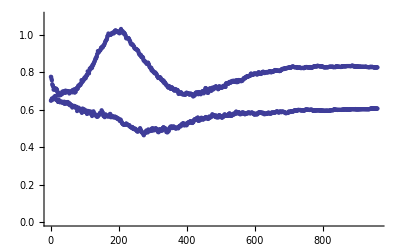

```mathematica
Show[ListPlot[MINorm,PlotRange->{{0,960},{0,1.1}}],ListPlot[MITN1R75OverHOfC,PlotRange->{{0,960},{0,1.1}}]]
```

```mathematica
AgentRecordingLength=13;NumRecordings=300;
TrialLogSize=Length[RecordingFiles[[1]]];
Agent="R";
firstTarget=2.5;lastTarget=7.5;
minCurrPos=0.0;maxCurrPos=10.0;
targetBinSize=0.1;posBinSize=0.1;
compBinSize=0.01;
WorldLength=10.0;
Components = {"t","S1","S2","S3","S4","N1","N2","N3","N4","N5","ML","MR","X","V"};
```

```mathematica
(*** Estimating Unconditional Mutual Information ***)(* Curr Position div by HofC*)
DateString[]
Comp="N1";Agent="R";
MINorm={};
start = 401; end = 1360;step=100;

For[time=start,time≤end,time=time+step,
	Print[time];
	CompVar={};CurrPosVar={};
	For[rec=1,rec≤NumRecordings,rec++,
		TrialData=RecordingFiles[[rec]];
		TimedRow=TrialData[[time]];
		CompPos=Position[Components,Comp][[1]][[1]];
		If [Agent=="R",
			offset=AgentRecordingLength,
			offset=0];
		CompValue=TimedRow[[offset+CompPos]];
		Xind=Position[Components,"X"][[1]][[1]];
		CurrPos=TimedRow[[offset+Xind]];
		CurrPosVar=Append[CurrPosVar,CurrPos];
	];
	
	CurrPosVals=Table[i,{i,minCurrPos,maxCurrPos,posBinSize}];
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	biVariates=Thread[{CurrPosVar,CompVar}];
	(*{plot,{bincounts}}=Reap[Histogram3D[biVariates,{{targetbins},{compbins}},
							Function[{xbins,ybins,counts},Sow[counts]]]];*)
	bincounts=BinCounts[biVariates,{minCurrPos,maxCurrPos+posBinSize,posBinSize},{0.0,1.0+compBinSize,compBinSize}];
	compvals=Table[i,{i,0,1,compBinSize}];
	CurrPoscomps=Table[{x,y},{x,CurrPosVals},{y,compvals}];
	fCurrPoscomps=Flatten[CurrPoscomps,1];
	fbincounts=Flatten[bincounts,1];
	(*fbincounts=fbincounts/Sum[fbincounts[[i]],{i,1,Length[fbincounts]}]//N;*)
	cofreqs=Thread[{fCurrPoscomps,fbincounts}];
	pCurrPosComp=Interpolation[cofreqs,InterpolationOrder->2];
	sumpCurrPosComp=Sum[pCurrPosComp[x,y],{x,CurrPosVals},{y,compvals}];

	(*{plot2,{bincounts2}}=Reap[Histogram[CompVar,{compbins},
							Function[{bins,counts},Sow[counts]]]];*)
	bincounts2 = BinCounts[CompVar,{0.0,1.0+compBinSize,compBinSize}];
	fbincounts2=Flatten[bincounts2,2];
	(*fbincounts2=fbincounts2/Sum[fbincounts2[[i]],{i,1,Length[fbincounts2]}]//N;*)
	freqs=Thread[{compvals,fbincounts2}];
	pComp=Interpolation[freqs,InterpolationOrder->2];
	sumpComp=Sum[pComp[x],{x,compvals}];

	CurrPosBins=Table[i,{i,minCurrPos,maxCurrPos+posBinSize,posBinSize}];
	bincounts = BinCounts[CurrPosVar,{minCurrPos,maxCurrPos+posBinSize,posBinSize}];
	fbincounts=Flatten[bincounts,2];
	freqs=Thread[{CurrPosVals,fbincounts}];
	pCurrPos=Interpolation[freqs,InterpolationOrder->2];
	sumpCurrPos=Sum[pCurrPos[x],{x,CurrPosVals}];

	HofC = 0.0;
	For[c=0,c≤1,c+=compBinSize,
		pc=pComp[c]/sumpComp;
		If[pc<10^-7,pc=0.0];
		If[pc==0.0,
			HofC+=0.0,
			HofC += -1*pc*Log[2,pc];
		];
	];

	Entr=0.0;
	For[p=minCurrPos,p≤maxCurrPos,p+=posBinSize,
	For[c=0,c≤1,c+=compBinSize,
		pp=pCurrPos[p]/sumpCurrPos;
		If[pp<10^-7,pp=0.0];
		ppc=pCurrPosComp[p,c]/sumpCurrPosComp;
		If[ppc<10^-7,ppc=0.0];
		pc=pComp[c];
		pc=pc/sumpComp;
		If[pc<10^-7,pc=0.0];
		If [ppc==0.0||pp==0.0||pc==0.0,
			Entr+=0.0,
			v=Log[2,ppc/(pp*pc)];
			If[v==Infinity,
				Entr+=0.0, 
				Entr+=ppc*v;
			];
		];
	];
	];
	If[HofC==0.0,MI=0.0,MI=Entr/HofC;];
	MINorm=Append[MINorm,MI];
	Print[MI];
];
DateString[]
```

```mathematica
AgentRecordingLength=13;NumRecordings=300;
TrialLogSize=Length[RecordingFiles[[1]]];
Agent="R";
firstTarget=2.5;lastTarget=7.5;
minCurrDtoT=-5.0;maxCurrDtoT=8.75;
targetBinSize=0.1;distBinSize=0.05;
compBinSize=0.01;
WorldLength=10.0;
Components = {"t","S1","S2","S3","S4","N1","N2","N3","N4","N5","ML","MR","X","V"};
```

```mathematica
(*** Estimating Unconditional Mutual Information ***)(* Curr Distance to target div by HofC*)
DateString[]
Comp="N5";Agent="R";
MINorm={};
start = 401; end = 1360;step=10;

For[time=start,time≤end,time=time+step,
	Print[time];
	CompVar={};CurrDistToTargetVar={};
	For[rec=1,rec≤NumRecordings,rec++,
		TrialData=RecordingFiles[[rec]];
		target=TrialData[[1]][[1]];
		TimedRow=TrialData[[time]];
		CompPos=Position[Components,Comp][[1]][[1]];
		If [Agent=="R",
			offset=AgentRecordingLength,
			offset=0];
		CompValue=TimedRow[[offset+CompPos]];
		Xind=Position[Components,"X"][[1]][[1]];
		CurrPos=TimedRow[[offset+Xind]];
		If[CurrPos≤1.25,
			CurrDist=Mod[CurrPos-target,10],
			CurrDist=CurrPos-target];
		If[CurrDist<minCurrDtoT,CurrDist=minCurrDtoT];
		CurrDistToTargetVar = Append[CurrDistToTargetVar,CurrDist];
		CompVar=Append[CompVar,CompValue];
	];
	
	CurrDtoTVals=Table[i,{i,minCurrDtoT,maxCurrDtoT,distBinSize}];
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	biVariates=Thread[{CurrDistToTargetVar,CompVar}];
	(*{plot,{bincounts}}=Reap[Histogram3D[biVariates,{{targetbins},{compbins}},
							Function[{xbins,ybins,counts},Sow[counts]]]];*)
	bincounts=BinCounts[biVariates,{minCurrDtoT,maxCurrDtoT+distBinSize,distBinSize},{0.0,1.0+compBinSize,compBinSize}];
	compvals=Table[i,{i,0,1,compBinSize}];
	CurrDtoTcomps=Table[{x,y},{x,CurrDtoTVals},{y,compvals}];
	fCurrDtoTcomps=Flatten[CurrDtoTcomps,1];
	fbincounts=Flatten[bincounts,1];
	(*fbincounts=fbincounts/Sum[fbincounts[[i]],{i,1,Length[fbincounts]}]//N;*)
	cofreqs=Thread[{fCurrDtoTcomps,fbincounts}];
	pCurrDtoTComp=Interpolation[cofreqs,InterpolationOrder->2];
	sumpCurrDtoTComp=Sum[pCurrDtoTComp[x,y],{x,CurrDtoTVals},{y,compvals}];

	(*{plot2,{bincounts2}}=Reap[Histogram[CompVar,{compbins},
							Function[{bins,counts},Sow[counts]]]];*)
	bincounts2 = BinCounts[CompVar,{0.0,1.0+compBinSize,compBinSize}];
	fbincounts2=Flatten[bincounts2,2];
	(*fbincounts2=fbincounts2/Sum[fbincounts2[[i]],{i,1,Length[fbincounts2]}]//N;*)
	freqs=Thread[{compvals,fbincounts2}];
	pComp=Interpolation[freqs,InterpolationOrder->2];
	sumpComp=Sum[pComp[x],{x,compvals}];

	CurrDtoTBins=Table[i,{i,minCurrDtoT,maxCurrDtoT+distBinSize,distBinSize}];
	bincounts = BinCounts[CurrDistToTargetVar,{minCurrDtoT,maxCurrDtoT+distBinSize,distBinSize}];
	fbincounts=Flatten[bincounts,2];
	freqs=Thread[{CurrDtoTVals,fbincounts}];
	pCurrDtoT=Interpolation[freqs,InterpolationOrder->2];
	sumpCurrDtoT=Sum[pCurrDtoT[x],{x,CurrDtoTVals}];

	HofC = 0.0;
	For[c=0,c≤1,c+=compBinSize,
		pc=pComp[c]/sumpComp;
		If[pc<10^-7,pc=0.0];
		If[pc==0.0,
			HofC+=0.0,
			HofC += -1*pc*Log[2,pc];
		];
	];

	Entr=0.0;
	For[d=minCurrDtoT,d≤maxCurrDtoT,d+=distBinSize,
	For[c=0,c≤1,c+=compBinSize,
		pd=pCurrDtoT[d]/sumpCurrDtoT;
		If[pd<10^-7,pd=0.0];
		pdc=pCurrDtoTComp[d,c]/sumpCurrDtoTComp;
		If[pdc<10^-7,pdc=0.0];
		pc=pComp[c];
		pc=pc/sumpComp;
		If[pc<10^-7,pc=0.0];
		If [pdc==0.0||pd==0.0||pc==0.0,
			Entr+=0.0,
			v=Log[2,pdc/(pd*pc)];
			If[v==Infinity,
				Entr+=0.0, 
				Entr+=pdc*v;
			];
		];
	];
	];
	If[HofC==0.0,MI=0.0,MI=Entr/HofC;];
	MINorm=Append[MINorm,MI];
	Print[MI];
];
DateString[]
```

Mon 12 Mar 2012 12:06:12

Mon 12 Mar 2012 12:08:42

```mathematica
MICurrDtoTN5R75OverHOfC=MINorm;
```

```mathematica
Save["MICurrDtoTN5R75OverHOfC.dat",MICurrDtoTN1R75OverHOfC];
```

```mathematica
Get["MICurrDtoTN1R75OverHOfC.dat"]
```

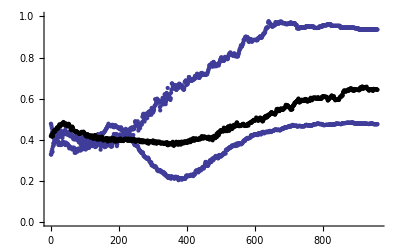

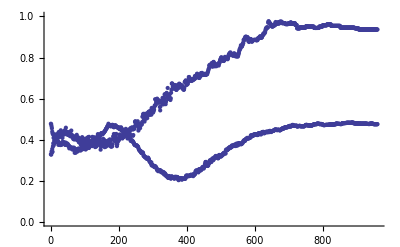

```mathematica
Show[ListPlot[MICurrDtoTN1R75OverHOfC,PlotRange->{{0,960},{0,1}}],ListPlot[MITN1R75OverHOfCCorrected,PlotRange->{{0,960},{0,1}}],ListPlot[MITN4R75OverHOfC,PlotRange->{{0,960},{0,1}},PlotStyle->{Black}]]
```

```mathematica
AgentRecordingLength=13;NumRecordings=300;
TrialLogSize=Length[RecordingFiles[[1]]];
Agent="R";
firstTarget=2.5;lastTarget=7.5;
minCurrDtoT=-5.0;maxCurrDtoT=8.75;
targetBinSize=0.1;distBinSize=0.05;
compBinSize=0.01;
WorldLength=10.0;
Components = {"t","S1","S2","S3","S4","N1","N2","N3","N4","N5","ML","MR","X","V"};
```

```mathematica
(*** Estimating Unconditional Mutual Information ***)(* Target Address div by HofC*)
DateString[]
Comp="N4";Agent="R";
MINorm={};
start = 401; end = 1360;step=1;

For[rec=1,rec≤NumRecordings,rec++,
	TrialData=RecordingFiles[[rec]];
	target=TrialData[[1]][[1]];
	TargetVar=Append[TargetVar,target];
];
targetvals=Table[i,{i,firstTarget,lastTarget,targetBinSize}];
Tbincounts = BinCounts[TargetVar,{firstTarget,lastTarget+targetBinSize,targetBinSize}];
fTbincounts=Flatten[Tbincounts,2];
Tfreqs=Thread[{targetvals,fTbincounts}];
pTarget=Interpolation[Tfreqs,InterpolationOrder->2];
sumpTarget=Sum[pTarget[x],{x,targetvals}];

For[time=start,time≤end,time=time+step,
	Print[time];
	TargetVar={};CompVar={};
	For[rec=1,rec≤NumRecordings,rec++,
		TrialData=RecordingFiles[[rec]];
		target=TrialData[[1]][[1]];
		TargetVar=Append[TargetVar,target];
		TimedRow=TrialData[[time]];
		CompPos=Position[Components,Comp][[1]][[1]];
		If [Agent=="R",
			offset=AgentRecordingLength,
			offset=0];
		CompValue=TimedRow[[offset+CompPos]];
		CompVar=Append[CompVar,CompValue];
	];
	
	targetbins=Table[i,{i,firstTarget,lastTarget+targetBinSize,targetBinSize}];
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	biVariates=Thread[{TargetVar,CompVar}];
	(*{plot,{bincounts}}=Reap[Histogram3D[biVariates,{{targetbins},{compbins}},
							Function[{xbins,ybins,counts},Sow[counts]]]];*)
	bincounts=BinCounts[biVariates,{firstTarget,lastTarget+targetBinSize,targetBinSize},{0.0,1.0+compBinSize,compBinSize}];
	targetvals=Table[i,{i,firstTarget,lastTarget,targetBinSize}];
	compvals=Table[i,{i,0,1,compBinSize}];
	tarscomps=Table[{x,y},{x,targetvals},{y,compvals}];
	ftarscomps=Flatten[tarscomps,1];
	fbincounts=Flatten[bincounts,1];
	(*fbincounts=fbincounts/Sum[fbincounts[[i]],{i,1,Length[fbincounts]}]//N;*)
	cofreqs=Thread[{ftarscomps,fbincounts}];
	pTargetComp=Interpolation[cofreqs,InterpolationOrder->2];
	sumpTargetComp=Sum[pTargetComp[x,y],{x,targetvals},{y,compvals}];

	(*{plot2,{bincounts2}}=Reap[Histogram[CompVar,{compbins},
							Function[{bins,counts},Sow[counts]]]];*)
	bincounts2 = BinCounts[CompVar,{0.0,1.0+compBinSize,compBinSize}];
	fbincounts2=Flatten[bincounts2,2];
	(*fbincounts2=fbincounts2/Sum[fbincounts2[[i]],{i,1,Length[fbincounts2]}]//N;*)
	freqs=Thread[{compvals,fbincounts2}];
	pComp=Interpolation[freqs,InterpolationOrder->2];
	sumpComp=Sum[pComp[x],{x,compvals}];

	HofC = 0.0;
	For[c=0,c≤1,c+=compBinSize,
		pc=pComp[c]/sumpComp;
		If[pc<10^-7,pc=0.0];
		If[pc==0.0,
			HofC+=0.0,
			HofC += -1*pc*Log[2,pc];
		];
	];

	Entr=0.0;
	(*pt=1/Length[targetvals];*)
	For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
	For[c=0,c≤1,c+=compBinSize,
		pt=pTarget[t]/sumpTarget;
		ptc=pTargetComp[t,c]/sumpTargetComp;
		If[ptc<10^-7,ptc=0.0];
		pc=pComp[c];
		pc=pc/sumpComp;
		If[pc<10^-7,pc=0.0];
		If [ptc==0.0||pt==0.0||pc==0.0,
			Entr+=0.0,
			v=Log[2,ptc/(pt*pc)];
			If[v==Infinity,
				Entr+=0.0, 
				Entr+=ptc*v;
			];
		];
	];
	];
	If[HofC>0.0,MI=Entr/HofC,MI=0.0];
	MINorm=Append[MINorm,MI];
	Print[MI];
];
DateString[]
```

Sun 11 Mar 2012 21:56:56

Sun 11 Mar 2012 22:01:14

```mathematica
MITN4R75OverHOfC=MINorm;
```

```mathematica
Save["MITN1R75OverHOfC.dat",MITN1R75OverHOfC];
```

```mathematica
AgentRecordingLength=13;NumRecordings=300;
TrialLogSize=Length[RecordingFiles[[1]]];
Agent="R";
firstTarget=2.5;lastTarget=7.5;
minCurrDtoT=-5.0;maxCurrDtoT=8.75;
(*minCurrDtoT=0.0;maxCurrDtoT=10.0;*)
targetBinSize=0.1;distBinSize=0.5;
compBinSize=0.01;
WorldLength=10.0;
Components = {"t","S1","S2","S3","S4","N1","N2","N3","N4","N5","ML","MR","X","V"};
```

```mathematica
(*** Estimating Conditional Mutual Information ***)(* I(N;CurrDtoT|TarAddr)/H(N|TarAddr) *)
DateString[]
Comp="N1";
start=1200;end=1200;step=100;
MINorm={}; TargetVar={};

For[rec=1,rec≤NumRecordings,rec++,
	TrialData=RecordingFiles[[rec]];
	target=TrialData[[1]][[1]];
	TargetVar=Append[TargetVar,target];
];
targetvals=Table[i,{i,firstTarget,lastTarget,targetBinSize}];
Tbincounts = BinCounts[TargetVar,{firstTarget,lastTarget+targetBinSize,targetBinSize}];
fTbincounts=Flatten[Tbincounts,2];
Tfreqs=Thread[{targetvals,fTbincounts}];
pTarget=Interpolation[Tfreqs,InterpolationOrder->2];
sumpTarget=Sum[pTarget[x],{x,targetvals}];

For[time=start,time≤end,time=time+step,
	Print[time];
	CompVar={};CurrDistToTargetVar={};
	For[rec=1,rec≤NumRecordings,rec++,
		TrialData=RecordingFiles[[rec]];
		target=TrialData[[1]][[1]];
		TimedRow=TrialData[[time]];
		CompPos=Position[Components,Comp][[1]][[1]];
		If[Agent=="R",
			CompValue=TimedRow[[AgentRecordingLength+CompPos]],
			CompValue=TimedRow[[CompPos]]
		];
		Xind=Position[Components,"X"][[1]][[1]];
		CurrPos=TimedRow[[AgentRecordingLength+Xind]];
		If[CurrPos≤1.25,
			CurrDist=Mod[CurrPos-target,10],
			CurrDist=CurrPos-target];
		If[CurrDist<minCurrDtoT,CurrDist=minCurrDtoT];
		CurrDistToTargetVar = Append[CurrDistToTargetVar,CurrDist];
		CompVar=Append[CompVar,CompValue];
	];
	
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	compTargetVariates=Thread[{CompVar,TargetVar}];
	CTbincounts=BinCounts[compTargetVariates,{0.0,1.0+compBinSize,compBinSize},
									                  {firstTarget,lastTarget+targetBinSize,targetBinSize}];
	compvals=Table[i,{i,0,1,compBinSize}];
	compstargets=Table[{x,y},{x,compvals},{y,targetvals}];
	fcompstargets=Flatten[compstargets,1];
	fCTbincounts=Flatten[CTbincounts,1];
	CTcofreqs=Thread[{fcompstargets,fCTbincounts}];
	pCompTarget=Interpolation[CTcofreqs,InterpolationOrder->2];
	sumpCompTarget=Sum[pCompTarget[x,y],{x,compvals},{y,targetvals}];

	EntropyCcondT=0.0;
	For[c=0.0,c≤1.0,c+=compBinSize,
	For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
	(*For[t=2.5,t≤2.5,t+=0.1,*)
		pct=pCompTarget[c,t]/sumpCompTarget;
		pt=pTarget[t]/sumpTarget;
		If[pct<10^-7,pct=0.0];
		If[pt<10^-7,pt=0.0];
		If[pct==0.0 || pt==0.0,
			EntropyCcondT-=0.0,
			EntropyCcondT-=pct*Log[2,pct/pt]
		];
	];
	];
	
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	CurrDtoTVals=Table[i,{i,minCurrDtoT,maxCurrDtoT,distBinSize}];
	CDTvariates=Thread[{CompVar,CurrDistToTargetVar,TargetVar}];
	CDTbincounts=BinCounts[CDTvariates,{0.0,1.0+compBinSize,compBinSize},{minCurrDtoT,maxCurrDtoT+distBinSize,distBinSize},
												{firstTarget,lastTarget+targetBinSize,targetBinSize}];
	CDTs=Table[{x,y,z},{x,compvals},{y,CurrDtoTVals},{z,targetvals}];
	fCDTs=Flatten[CDTs,2];
	fCDTbincounts=Flatten[CDTbincounts,2];
	CDTcofreqs=Thread[{fCDTs,fCDTbincounts}];
	pCDT=Interpolation[CDTcofreqs,InterpolationOrder->2];
	sumpCDT=Sum[pCDT[x,y,z],{x,compvals},{y,CurrDtoTVals},{z,targetvals}];
	
	diststargets=Table[{x,y},{x,CurrDtoTVals},{y,targetvals}];
	fdiststargets=Flatten[diststargets,1];
	distTargetVariates=Thread[{CurrDistToTargetVar,TargetVar}];
	DTbincounts=BinCounts[distTargetVariates,{minCurrDtoT,maxCurrDtoT+distBinSize,distBinSize},
									                  {firstTarget,lastTarget+targetBinSize,targetBinSize}];
	fDTbincounts=Flatten[DTbincounts,1];
	DTcofreqs=Thread[{fdiststargets,fDTbincounts}];
	pCurrDtoTTarget=Interpolation[DTcofreqs,InterpolationOrder->2];
	sumpCurrDtoTTarget=Sum[pCurrDtoTTarget[x,y],{x,CurrDtoTVals},{y,targetvals}];

	Entr=0.0;
	For[d=minCurrDtoT,d≤maxCurrDtoT,d+=distBinSize,
	For[c=0.0,c≤1.0,c+=compBinSize,
	(*For[t=7.5,t≤7.5,t+=0.1,*)
	For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
		pcdt=pCDT[c,d,t]/sumpCDT;
		pct=pCompTarget[c,t]/sumpCompTarget;
		pdt=pCurrDtoTTarget[d,t]/sumpCurrDtoTTarget;
		pt=pTarget[t]/sumpTarget;
		If[pcdt<10^-7,pcdt=0.0];
		If[pct<10^-7,pct=0.0];
		If[pdt<10^-7,pdt=0.0];
		If[pt<10^-7,pt=0.0];
		If [pcdt==0.0||pct==0.0||pdt==0.0 || pt==0.0,
			Entr+=0.0,
			v=Log[2,(pcdt*pt)/(pct*pdt)];
			If[v==Infinity,
				Print[v];Entr+=0.0, 
				Entr+=pcdt*v;
			];
		];
	];
	];
	];
	MI=Entr/EntropyCcondT;
	MINorm=Append[MINorm,MI];
	Print[MI];
];
DateString[]
```

Mon 12 Mar 2012 13:10:50

1200

0.497675

Mon 12 Mar 2012 13:11:03

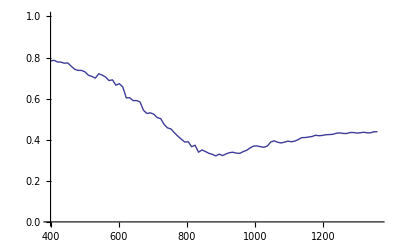

```mathematica
ListPlot[MICurrDtoTN1R75OverHOfC,DataRange->{400,1360},PlotRange->{{400,1360},{0,1}},Joined->True]
```

```mathematica
Show[ListPlot[MICurrDtoTN1R75OverHOfC,DataRange->{400,1360},PlotRange->{{400,1360},{0,1}},Joined->True,PlotStyle->{Thick,Black,Dashing[Tiny]}],ListPlot[MIN1CurrDtoTCondTR75OverHofCcondT,DataRange->{400,1360},PlotRange->{{400,1360},{0,1}},Joined->True,PlotStyle->{Thickness[0.003],Black,Dashing[0.01]}],ListPlot[MITN1R75OverHOfCCorrected,DataRange->{400,1360},PlotRange->{{400,1360},{0,1}},Joined->True,PlotStyle->{Black}],AxesLabel->{"Time","Normalized Mutual Information"}]
```

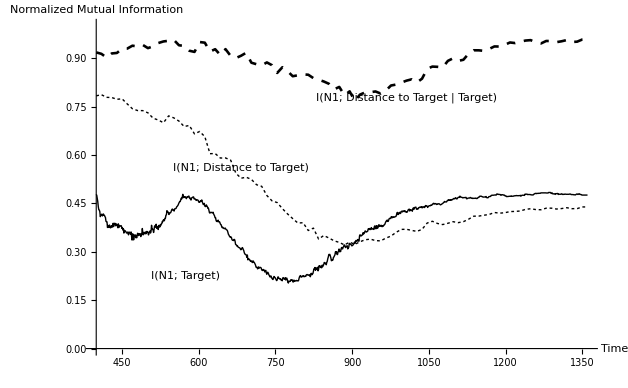

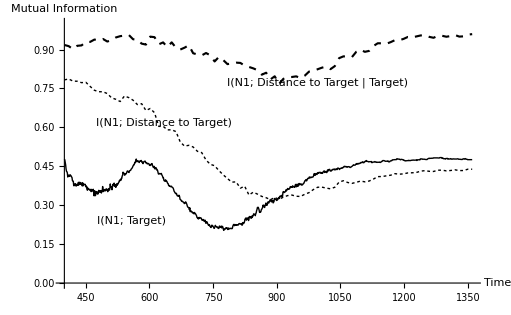

```mathematica
MIN1CurrDtoTCondTR75OverHofCcondT=MINorm;
```

```mathematica
Save["MIN1CurrDtoTCondTR75OverHofCcondT.dat",MIN1CurrDtoTCondTR75OverHofCcondT];
```

```mathematica
AgentRecordingLength=13;NumRecordings=300;
TrialLogSize=Length[RecordingFiles[[1]]];
Agent="R";
firstTarget=-5.0;lastTarget=8.7;
minCurrDtoT=0.0;maxCurrDtoT=1.0;
(*minCurrDtoT=0.0;maxCurrDtoT=10.0;*)
targetBinSize=0.3;distBinSize=0.01;compBinSize=0.01;
Components = {"t","S1","S2","S3","S4","N1","N2","N3","N4","N5","ML","MR","X","V"};
```

```mathematica
(*** Estimating Conditional Mutual Information ***)(* I(N;CurrDtoT|TarAddr)/H(N|TarAddr) *)
DateString[]
Comp="ML";Ncomp="N1";
start=401;end=900;step=10;
MINorm={}; 

For[time=start,time≤end,time=time+step,
	Print[time];
	CompVar={};CurrDistToTargetVar={};TargetVar={};
	For[rec=1,rec≤NumRecordings,rec++,
		TrialData=RecordingFiles[[rec]];
		target=TrialData[[1]][[1]];
		TimedRow=TrialData[[time]];
		CompPos=Position[Components,Comp][[1]][[1]];
		If[Agent=="R",
			CompValue=TimedRow[[AgentRecordingLength+CompPos]],
			CompValue=TimedRow[[CompPos]]
		];
		CompVar=Append[CompVar,CompValue]; (*ML value*)
		Nind=Position[Components,Ncomp][[1]][[1]];
		Nvalue=TimedRow[[AgentRecordingLength+Nind]]; (*N value*)
		CurrDistToTargetVar = Append[CurrDistToTargetVar,Nvalue];
		Xind=Position[Components,"X"][[1]][[1]];
		CurrPos=TimedRow[[AgentRecordingLength+Xind]];
		If[CurrPos≤1.25,
			CurrDist=Mod[CurrPos-target,10],
			CurrDist=CurrPos-target];
		If[CurrDist<firstTarget,CurrDist=firstTarget];
		TargetVar = Append[TargetVar,CurrDist];
	];

	targetvals=Table[i,{i,firstTarget,lastTarget,targetBinSize}];
	Tbincounts = BinCounts[TargetVar,{firstTarget,lastTarget+targetBinSize,targetBinSize}];
	fTbincounts=Flatten[Tbincounts,2];
	Tfreqs=Thread[{targetvals,fTbincounts}];
	pTarget=Interpolation[Tfreqs,InterpolationOrder->2];
	sumpTarget=Sum[pTarget[x],{x,targetvals}];
	
	compTargetVariates=Thread[{CompVar,TargetVar}];
	CTbincounts=BinCounts[compTargetVariates,{0.0,1.0+compBinSize,compBinSize},
									                  {firstTarget,lastTarget+targetBinSize,targetBinSize}];
	compvals=Table[i,{i,0,1,compBinSize}];
	compstargets=Table[{x,y},{x,compvals},{y,targetvals}];
	fcompstargets=Flatten[compstargets,1];
	fCTbincounts=Flatten[CTbincounts,1];
	CTcofreqs=Thread[{fcompstargets,fCTbincounts}];
	pCompTarget=Interpolation[CTcofreqs,InterpolationOrder->2];
	sumpCompTarget=Sum[pCompTarget[x,y],{x,compvals},{y,targetvals}];

	EntropyCcondT=0.0;
	For[c=0.0,c≤1.0,c+=compBinSize,
	(*For[t=firstTarget,t≤lastTarget,t+=targetBinSize,*)
	For[t=-2.0,t≤2.0,t+=targetBinSize,
		pct=pCompTarget[c,t]/sumpCompTarget;
		pt=pTarget[t]/sumpTarget;
		If[pct<10^-7,pct=0.0];
		If[pt<10^-7,pt=0.0];
		If[pct==0.0 || pt==0.0,
			EntropyCcondT-=0.0,
			EntropyCcondT-=pct*Log[2,pct/pt]
		];
	];
	];
	
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	CurrDtoTVals=Table[i,{i,minCurrDtoT,maxCurrDtoT,distBinSize}];
	CDTvariates=Thread[{CompVar,CurrDistToTargetVar,TargetVar}];
	CDTbincounts=BinCounts[CDTvariates,{0.0,1.0+compBinSize,compBinSize},{minCurrDtoT,maxCurrDtoT+distBinSize,distBinSize},
												{firstTarget,lastTarget+targetBinSize,targetBinSize}];
	CDTs=Table[{x,y,z},{x,compvals},{y,CurrDtoTVals},{z,targetvals}];
	fCDTs=Flatten[CDTs,2];
	fCDTbincounts=Flatten[CDTbincounts,2];
	CDTcofreqs=Thread[{fCDTs,fCDTbincounts}];
	pCDT=Interpolation[CDTcofreqs,InterpolationOrder->2];
	sumpCDT=Sum[pCDT[x,y,z],{x,compvals},{y,CurrDtoTVals},{z,targetvals}];
	
	diststargets=Table[{x,y},{x,CurrDtoTVals},{y,targetvals}];
	fdiststargets=Flatten[diststargets,1];
	distTargetVariates=Thread[{CurrDistToTargetVar,TargetVar}];
	DTbincounts=BinCounts[distTargetVariates,{minCurrDtoT,maxCurrDtoT+distBinSize,distBinSize},
									                  {firstTarget,lastTarget+targetBinSize,targetBinSize}];
	fDTbincounts=Flatten[DTbincounts,1];
	DTcofreqs=Thread[{fdiststargets,fDTbincounts}];
	pCurrDtoTTarget=Interpolation[DTcofreqs,InterpolationOrder->2];
	sumpCurrDtoTTarget=Sum[pCurrDtoTTarget[x,y],{x,CurrDtoTVals},{y,targetvals}];

	Entr=0.0;
	For[d=minCurrDtoT,d≤maxCurrDtoT,d+=distBinSize,
	For[c=0.0,c≤1.0,c+=compBinSize,
	For[t=-2.0,t≤2.0,t+=targetBinSize,
	(*For[t=firstTarget,t≤lastTarget,t+=targetBinSize,*)
		pcdt=pCDT[c,d,t]/sumpCDT;
		pct=pCompTarget[c,t]/sumpCompTarget;
		pdt=pCurrDtoTTarget[d,t]/sumpCurrDtoTTarget;
		pt=pTarget[t]/sumpTarget;
		If[pcdt<10^-7,pcdt=0.0];
		If[pct<10^-7,pct=0.0];
		If[pdt<10^-7,pdt=0.0];
		If[pt<10^-7,pt=0.0];
		If [pcdt==0.0||pct==0.0||pdt==0.0 || pt==0.0,
			Entr+=0.0,
			v=Log[2,(pcdt*pt)/(pct*pdt)];
			If[v==Infinity,
				Print[v];Entr+=0.0, 
				Entr+=pcdt*v;
			];
		];
	];
	];
	];
	MI=Entr/EntropyCcondT;
	MINorm=Append[MINorm,MI];
	Print[MI];
];
DateString[]
```

Mon 12 Mar 2012 16:00:45

Mon 12 Mar 2012 16:18:17

```mathematica
MIMLN1CondCurrDtoTOverHofMLCondCurrDtoT=MINorm;
```

```mathematica
Save["MIMLN1CondCurrDtoTOverHofMLCondCurrDtoT.dat",MIMLN1CondCurrDtoTOverHofMLCondCurrDtoT];
```

```mathematica
Show[ListPlot[MIMLN1CondCurrDtoTOverHofMLCondCurrDtoT,DataRange->{400,900},PlotRange->{{400,900},{0,1}},Joined->True,PlotStyle->{Thick,Black,Dashing[Tiny]}],ListPlot[MIMLN5CondCurrDtoTOverHofMLCondCurrDtoT,DataRange->{400,900},PlotRange->{{400,900},{0,1}},Joined->True,PlotStyle->{Thickness[0.003],Black,Dashing[0.01]}],AxesLabel->{"Time","Normalized Mutual Information"}]
```

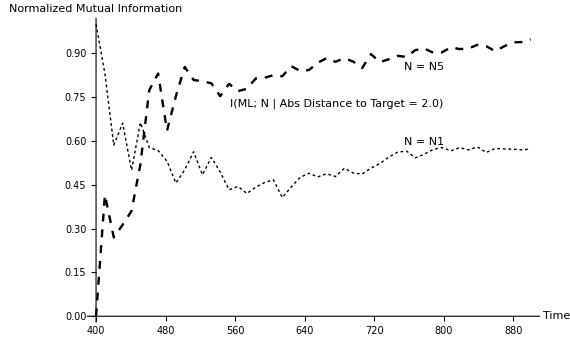

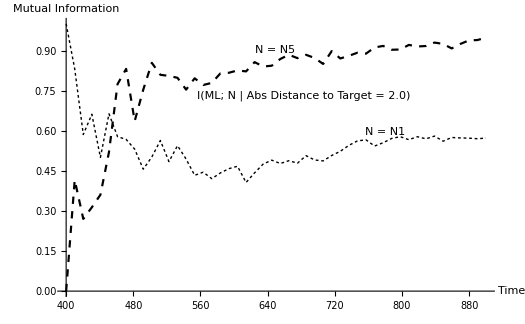

```mathematica
ipf=Interpolation[CTcofreqs,InterpolationOrder->2]
```

InterpolatingFunction[{{0.,1.},{-5.,8.5}},<>]

```mathematica
ipf[0,-5]
```

0.

```mathematica
Length[fCTbincounts]
```

4646

```mathematica
Table[{i+10,i},{i,25}]
```

{{11,1},{12,2},{13,3},{14,4},{15,5},{16,6},{17,7},{18,8},{19,9},{20,10},{21,11},{22,12},{23,13},{24,14},{25,15},{26,16},{27,17},{28,18},{29,19},{30,20},{31,21},{32,22},{33,23},{34,24},{35,25}}

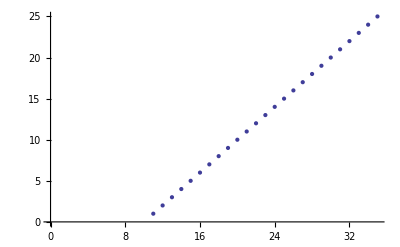

```mathematica
ListPlot[Table[{i+10,i},{i,25}],AxesOrigin->{0,0},DataRange->{0,1}]
```

```mathematica
TargetVar
```

{2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.5,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,2.85714,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.21429,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.57143,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,3.92857,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.28571,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,4.64286,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.35714,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,5.71429,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.07143,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.42857,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,6.78571,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.14286,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5}

```mathematica
Max[CurrDistToTargetVar]
```

8.71875

```mathematica
Entr=0.0;
	For[d=minCurrDtoT,d≤maxCurrDtoT,d+=distBinSize,
	For[c=0.0,c≤1.0,c+=compBinSize,
	For[t=5,t≤5,t+=0.1,
	(*For[t=firstTarget,t≤lastTarget,t+=targetBinSize,*)
		pcdt=pCDT[c,d,t]/sumpCDT;
		pct=pCompTarget[c,t]/sumpCompTarget;
		pdt=pCurrDtoTTarget[d,t]/sumpCurrDtoTTarget;
		pt=pTarget[t]/sumpTarget;
		If[pcdt<10^-7,pcdt=0.0];
		If[pct<10^-7,pct=0.0];
		If[pdt<10^-7,pdt=0.0];
		If[pt<10^-7,pt=0.0];
		If [pcdt==0.0||pct==0.0||pdt==0.0 || pt==0.0,
			Entr+=0.0,
			v=Log[2,(pcdt*pt)/(pct*pdt)];
			If[v==Infinity,
				Print[v];Entr+=0.0, 
				Entr+=pcdt*v;
			];
		];
	];
	];
	];
	MI=Entr/EntropyCcondT;
```

```mathematica
MI
```

0.0681195

```mathematica
EntropyCcondT
```

2.74138

```mathematica
0.91*3.07
```

2.7937

```mathematica
0.91*0.19
```

0.1729

Sun 11 Mar 2012 22:11:09

401

0.913401

406

0.930276

411

0.921006

416

0.888552

421

0.920483

426

0.926789

431

0.931252

436

0.922688

441

0.927671

446

0.917761

451

0.925278

456

0.926038

461

0.937532

466

0.922114

471

0.935756

476

0.945017

481

0.881618

486

0.951347

491

0.916741

496

0.913555

501

0.928558

506

0.929759

511

$Aborted

Mon 12 Mar 2012 00:10:45

```mathematica
MINorm
```

```mathematica
MINorm2={0.952280221353318,0.9437846465817641,0.9687182642587946,0.9478177492343902,0.9516630172754711,0.9390339905653493,0.9473602646481609,0.9435478372190198}
```

{0.95228,0.943785,0.968718,0.947818,0.951663,0.939034,0.94736,0.943548}

```mathematica
MINorm1={0.9134011609351289,0.9302757518007152,0.9210060938597846,0.8885524907713394,0.9204829810692879,0.9267885862448286,0.9312523457382971,0.9226875320815446,0.9276714188713995,0.9177608884636161,0.9252780657052928,0.9260377429719863,0.9375319030030393,0.92211410424068,0.9357562386808572,0.9450169529366695,0.8816180953948608,0.9513465732251546,0.9167414295623141,0.9135547447957285,0.9285579997089611,0.9297587695258509};
```

```mathematica
MINorm1
```

{0.913401,0.930276,0.921006,0.888552,0.920483,0.926789,0.931252,0.922688,0.927671,0.917761,0.925278,0.926038,0.937532,0.922114,0.935756,0.945017,0.881618,0.951347,0.916741,0.913555,0.928558,0.929759}

```mathematica
pTarget[5.3]/sumpTarget
```

0.0666667

```mathematica
MITN1R75OverHOfC=MINorm;
```

```mathematica
Save["MITN1R75OverHOfC.dat",MITN1R75OverHOfC];
```

```mathematica
(*** Estimating Unconditional Mutual Information ***)(* Distance to target div by HofDtoT*)
DateString[]
Comp="N1";Agent="R";
MINorm={};
start = 401; end = 1360;step=1;

DistToTargetVar={};
For[rec=1,rec≤NumRecordings,rec++,
	TrialData=RecordingFiles[[rec]];
	target=TrialData[[1]][[1]];
	FirstTrialRow=TrialData[[start]];
	XPos=Position[Components,"X"][[1]][[1]];
	InitPos=FirstTrialRow[[offset+XPos]];
	DistToTargetVar = Append[DistToTargetVar,Mod[InitPos-target,10]];
];

DtoTVals=Table[i,{i,minDtoT,maxDtoT,distBinSize}];
DtoTBins=Table[i,{i,minDtoT,maxDtoT+distBinSize,distBinSize}];
bincounts = BinCounts[DistToTargetVar,{minDtoT,maxDtoT+distBinSize,distBinSize}];
fbincounts=Flatten[bincounts,2];
freqs=Thread[{DtoTVals,fbincounts}];
pDtoT=Interpolation[freqs,InterpolationOrder->2];
sumpDtoT=Sum[pDtoT[x],{x,DtoTVals}];
	
HofDtoT = 0.0;
For[d=minDtoT,d≤maxDtoT,d+=distBinSize,
	pd=pDtoT[d]/sumpDtoT;
	If[pd<10^-7,pd=0.0];
	If[pd==0.0,
		HofDtoT+=0.0,
		HofDtoT += -1*pd*Log[2,pd];
	];
];

For[time=start,time≤end,time=time+step,
	Print[time];
	CompVar={};
	For[rec=1,rec≤NumRecordings,rec++,
		TrialData=RecordingFiles[[rec]];
		TimedRow=TrialData[[time]];
		CompPos=Position[Components,Comp][[1]][[1]];
		If [Agent=="R",
			offset=AgentRecordingLength,
			offset=0];
		CompValue=TimedRow[[offset+CompPos]];
		CompVar=Append[CompVar,CompValue];
	];
	
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	biVariates=Thread[{DistToTargetVar,CompVar}];
	(*{plot,{bincounts}}=Reap[Histogram3D[biVariates,{{targetbins},{compbins}},
							Function[{xbins,ybins,counts},Sow[counts]]]];*)
	bincounts=BinCounts[biVariates,{minDtoT,maxDtoT+distBinSize,distBinSize},{0.0,1.0+compBinSize,compBinSize}];
	compvals=Table[i,{i,0,1,compBinSize}];
	DtoTcomps=Table[{x,y},{x,DtoTVals},{y,compvals}];
	fDtoTcomps=Flatten[DtoTcomps,1];
	fbincounts=Flatten[bincounts,1];
	(*fbincounts=fbincounts/Sum[fbincounts[[i]],{i,1,Length[fbincounts]}]//N;*)
	cofreqs=Thread[{fDtoTcomps,fbincounts}];
	pDtoTComp=Interpolation[cofreqs,InterpolationOrder->2];
	sumpDtoTComp=Sum[pDtoTComp[x,y],{x,DtoTVals},{y,compvals}];

	(*{plot2,{bincounts2}}=Reap[Histogram[CompVar,{compbins},
							Function[{bins,counts},Sow[counts]]]];*)
	bincounts2 = BinCounts[CompVar,{0.0,1.0+compBinSize,compBinSize}];
	fbincounts2=Flatten[bincounts2,2];
	(*fbincounts2=fbincounts2/Sum[fbincounts2[[i]],{i,1,Length[fbincounts2]}]//N;*)
	freqs=Thread[{compvals,fbincounts2}];
	pComp=Interpolation[freqs,InterpolationOrder->2];
	sumpComp=Sum[pComp[x],{x,compvals}];

	Entr=0.0;
	For[d=minDtoT,d≤maxDtoT,d+=distBinSize,
	For[c=0,c≤1,c+=compBinSize,
		pd=pDtoT[d]/sumpDtoT;
		If[pd<10^-7,pd=0.0];
		pdc=pDtoTComp[d,c]/sumpDtoTComp;
		If[pdc<10^-7,pdc=0.0];
		pc=pComp[c];
		pc=pc/sumpComp;
		If[pc<10^-7,pc=0.0];
		If [pdc==0.0||pd==0.0||pc==0.0,
			Entr+=0.0,
			v=Log[2,pdc/(pd*pc)];
			If[v==Infinity,
				Entr+=0.0, 
				Entr+=pdc*v;
			];
		];
	];
	];
	MI=Entr/HofDtoT;
	MINorm=Append[MINorm,MI];
	Print[MI];
];
DateString[]
```

Sun 11 Mar 2012 13:14:50

Sun 11 Mar 2012 13:25:47

```mathematica
MIDtoTN1R75OverHOfDtoT=MINorm;
Save["MIDtoTN1R75OverHOfDtoT.dat",MIDtoTN1R75OverHOfDtoT];
```

```mathematica
Get["MITN1R75Cou.dat"]
```

```mathematica
$Path
```

{/Applications/Mathematica.app/SystemFiles/Links,/Users/smanicka/Library/Mathematica/Kernel,/Users/smanicka/Library/Mathematica/Autoload,/Users/smanicka/Library/Mathematica/Applications,/Library/Mathematica/Kernel,/Library/Mathematica/Autoload,/Library/Mathematica/Applications,.,/Users/smanicka,/Applications/Mathematica.app/AddOns/Packages,/Applications/Mathematica.app/AddOns/LegacyPackages,/Applications/Mathematica.app/SystemFiles/Autoload,/Applications/Mathematica.app/AddOns/Autoload,/Applications/Mathematica.app/AddOns/Applications,/Applications/Mathematica.app/AddOns/ExtraPackages,/Applications/Mathematica.app/SystemFiles/Kernel/Packages,/Applications/Mathematica.app/Documentation/English/System,/Users/smanicka/Documents/My IU/Fall 2011/Q700 Evol and anal/Final project/Analysis/,/Users/smanicka/Documents/My IU/Fall 2011/Q700 Evol and anal/Final project/Analysis/}

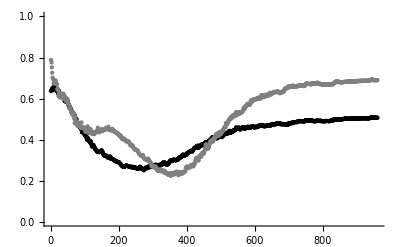

```mathematica
Show[ListPlot[MINorm,PlotRange->{{0,960},{0,1}},PlotStyle->{Black}],ListPlot[MITN1R75Cou,PlotRange->{{0,960},{0,1}},PlotStyle->{Gray}]]
```

```mathematica
N[Log[2,15]]
```

3.90689

```mathematica
HofDtoT
```

6.00528

Sun 11 Mar 2012 13:46:09

Sun 11 Mar 2012 13:46:12

```mathematica
(*** Estimating Unconditional Mutual Information ***)(* Target Address div by HofT*)
DateString[]
Comp="ML";Agent="R";
MINorm={};
start = 401; end = 1360;
For[time=start,time≤end,time=time+100,
	Print[time];
	TargetVar={};CompVar={};
	For[rec=1,rec≤NumRecordings,rec++,
		TrialData=RecordingFiles[[rec]];
		target=TrialData[[1]][[1]];
		TargetVar=Append[TargetVar,target];
		TimedRow=TrialData[[time]];
		CompPos=Position[Components,Comp][[1]][[1]];
		If [Agent=="R",
			offset=AgentRecordingLength,
			offset=0];
		CompValue=TimedRow[[offset+CompPos]];
		CompVar=Append[CompVar,CompValue];
	];
	
	targetbins=Table[i,{i,firstTarget,lastTarget+targetBinSize,targetBinSize}];
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	biVariates=Thread[{TargetVar,CompVar}];
	(*{plot,{bincounts}}=Reap[Histogram3D[biVariates,{{targetbins},{compbins}},
							Function[{xbins,ybins,counts},Sow[counts]]]];*)
	bincounts=BinCounts[biVariates,{firstTarget,lastTarget+targetBinSize,targetBinSize},{0.0,1.0+compBinSize,compBinSize}];
	targetvals=Table[i,{i,firstTarget,lastTarget,targetBinSize}];
	compvals=Table[i,{i,0,1,compBinSize}];
	tarscomps=Table[{x,y},{x,targetvals},{y,compvals}];
	ftarscomps=Flatten[tarscomps,1];
	fbincounts=Flatten[bincounts,1];
	(*fbincounts=fbincounts/Sum[fbincounts[[i]],{i,1,Length[fbincounts]}]//N;*)
	cofreqs=Thread[{ftarscomps,fbincounts}];
	pTargetComp=Interpolation[cofreqs,InterpolationOrder->2];
	sumpTargetComp=Sum[pTargetComp[x,y],{x,targetvals},{y,compvals}];

	(*{plot2,{bincounts2}}=Reap[Histogram[CompVar,{compbins},
							Function[{bins,counts},Sow[counts]]]];*)
	bincounts2 = BinCounts[CompVar,{0.0,1.0+compBinSize,compBinSize}];
	fbincounts2=Flatten[bincounts2,2];
	(*fbincounts2=fbincounts2/Sum[fbincounts2[[i]],{i,1,Length[fbincounts2]}]//N;*)
	freqs=Thread[{compvals,fbincounts2}];
	pComp=Interpolation[freqs,InterpolationOrder->2];
	sumpComp=Sum[pComp[x],{x,compvals}];

	Entr=0.0;
	pt=1/Length[targetvals];
	For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
	For[c=0,c≤1,c+=compBinSize,
		ptc=pTargetComp[t,c]/sumpTargetComp;
		If[ptc<10^-7,ptc=0.0];
		pc=pComp[c];
		pc=pc/sumpComp;
		If[pc<10^-7,pc=0.0];
		If [ptc==0.0||pt==0.0||pc==0.0,
			Entr+=0.0,
			v=Log[2,ptc/(pt*pc)];
			If[v==Infinity,
				Entr+=0.0, 
				Entr+=ptc*v;
			];
		];
	];
	];
	(*MI=Entr/Log[2,Length[targetvals]];*)
	MI = Entr;
	MINorm=Append[MINorm,MI];
	Print[MI];
];
DateString[]
```

Mon 5 Mar 2012 00:05:54

Mon 5 Mar 2012 00:05:56

```mathematica
Mod[8.75-7.5,10]
```

1.25

8.75

```mathematica
MITMLR75New=MINorm;
```

```mathematica
RecordingFiles=RecordingFiles75;
RecordingFilesROnly=RecordingFilesROnly75;
```

```mathematica
AgentRecordingLength=13;NumRecordings=300;PreTrial=60;
TrialLogSize=Length[RecordingFiles[[1]]];
Agent="R";
firstTarget=2.5;
lastTarget=7.5;
targetBinSize=0.1;
intrinsicBinSize=0.1;
compBinSize=0.01;
WorldLength=10.0;
Components = {"t","S1","S2","S3","S4","N1","N2","N3","N4","N5","ML","MR","X","V"};
```

```mathematica
(*** Estimating Conditional Mutual Information ***)
DateString[]
Comp="ML";
(*EndTime=PreTrial/0.1;*)
MINorm={};IntrinsicTargetVar={};TargetVar={};
For[rec=1,rec≤NumRecordings,rec++,
	TrialData=RecordingFiles[[rec]];
	target=TrialData[[1]][[1]];
	TargetVar=Append[TargetVar,target];
	(*LastRow=TrialData[[TrialLogSize]];
	CompPos=Position[Components,"X"][[1]][[1]];
	ActualFinalPos=LastRow[[AgentRecordingLength+CompPos]];*)
	FirstTrialRow=TrialData[[3]];
	CompPos=Position[Components,"X"][[1]][[1]];
	InitPos=FirstTrialRow[[AgentRecordingLength+CompPos]];
	TrialData=RecordingFilesROnly[[rec]];
	LastRow=TrialData[[TrialLogSize]];
	CompPos=Position[Components,"X"][[1]][[1]];
	intrinsicTarget=LastRow[[AgentRecordingLength+CompPos]];
	DistToTravel = InitPos - target;
	If[DistToTravel<0.0,DistToTravel=10+DistToTravel];
	IntrinsicTargetVar=Append[IntrinsicTargetVar,DistToTravel];
	(*IntrinsicTargetVar=Append[IntrinsicTargetVar,Abs[target-intrinsicTarget]];*)
	(*IntrinsicTargetVar=Append[IntrinsicTargetVar,target-intrinsicTarget];*)
	(*lDist = Abs[ActualFinalPos-intrinsicTarget];
	rDist = 10-lDist;
	ActIntDist = Min[lDist,rDist];
	IntrinsicTargetVar=Append[IntrinsicTargetVar,ActIntDist];*)
	(*IntrinsicTargetVar=Append[IntrinsicTargetVar,ActualFinalPos]*)
	(*IntrinsicTargetVar=Append[IntrinsicTargetVar,intrinsicTarget];*)
];
targetbins=Table[i,{i,firstTarget,lastTarget+targetBinSize,targetBinSize}];
intrinsicbins=Table[i,{i,0.0,WorldLength+intrinsicBinSize,intrinsicBinSize}];
intrinsicTargetVariates=Thread[{IntrinsicTargetVar,TargetVar}];
ITbincounts=BinCounts[intrinsicTargetVariates,{0.0,WorldLength+intrinsicBinSize,intrinsicBinSize},
												{firstTarget,lastTarget+targetBinSize,targetBinSize}];
targetvals=Table[i,{i,firstTarget,lastTarget,targetBinSize}];
intrinsicvals=Table[i,{i,0.0,WorldLength,intrinsicBinSize}];
intrinstargets=Table[{x,y},{x,intrinsicvals},{y,targetvals}];
fintrinstargets=Flatten[intrinstargets,1];
fITbincounts=Flatten[ITbincounts,1];
ITcofreqs=Thread[{fintrinstargets,fITbincounts}];
pIntrinsicTarget=Interpolation[ITcofreqs,InterpolationOrder->2];
sumpIntrinsicTarget=Sum[pIntrinsicTarget[x,y],{x,intrinsicvals},{y,targetvals}];

Ibincounts = BinCounts[IntrinsicTargetVar,{0.0,WorldLength+intrinsicBinSize,intrinsicBinSize}];
fIbincounts=Flatten[Ibincounts,2];
Ifreqs=Thread[{intrinsicvals,fIbincounts}];
pIntrinsic=Interpolation[Ifreqs,InterpolationOrder->2];
sumpIntrinsic=Sum[pIntrinsic[x],{x,intrinsicvals}];

(*EntropyTcondI=0.0;
For[i=-WorldLength,i≤WorldLength,i+=intrinsicBinSize,
For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
	pit=pIntrinsicTarget[i,t]/sumpIntrinsicTarget;
	pi=pIntrinsic[i]/sumpIntrinsic;
	If[pit<10^-7,pit=0.0];
	If[pi<10^-7,pi=0.0];
	If[pit==0.0,
		EntropyTcondI-=0.0,
		EntropyTcondI-=pit*Log[2,pit/pi]
	];
];
];*)

For[time=401,time≤1360,time=time+100,
	Print[time];
	CompVar={};
	For[rec=1,rec≤NumRecordings,rec++,
		TrialData=RecordingFiles[[rec]];
		TimedRow=TrialData[[time]];
		CompPos=Position[Components,Comp][[1]][[1]];
		If[Agent=="R",
			CompValue=TimedRow[[AgentRecordingLength+CompPos]],
			CompValue=TimedRow[[CompPos]]
		];
		CompVar=Append[CompVar,CompValue];
	];
	
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	IntrinsicCompVariates=Thread[{IntrinsicTargetVar,CompVar}];
	ICTvariates=Thread[{IntrinsicTargetVar,CompVar,TargetVar}];
	ICbincounts=BinCounts[IntrinsicCompVariates,{0.0,WorldLength+intrinsicBinSize,intrinsicBinSize},{0.0,1.0+compBinSize,compBinSize}];
	ICTbincounts=BinCounts[ICTvariates,{0.0,WorldLength+intrinsicBinSize,intrinsicBinSize},{0.0,1.0+compBinSize,compBinSize},
												{firstTarget,lastTarget+targetBinSize,targetBinSize}];
	compvals=Table[i,{i,0.0,1.0,compBinSize}];
	intrinscomps=Table[{x,y},{x,intrinsicvals},{y,compvals}];
	ICTs=Table[{x,y,z},{x,intrinsicvals},{y,compvals},{z,targetvals}];
	fintrinscomps=Flatten[intrinscomps,1];
	fICTs=Flatten[ICTs,2];
	fICbincounts=Flatten[ICbincounts,1];
	fICTbincounts=Flatten[ICTbincounts,2];
	ICcofreqs=Thread[{fintrinscomps,fICbincounts}];
	ICTcofreqs=Thread[{fICTs,fICTbincounts}];
	pIntrinsicComp=Interpolation[ICcofreqs,InterpolationOrder->2];
	pICT=Interpolation[ICTcofreqs,InterpolationOrder->2];
	sumpIntrinsicComp=Sum[pIntrinsicComp[x,y],{x,intrinsicvals},{y,compvals}];
	sumpICT=Sum[pICT[x,y,z],{x,intrinsicvals},{y,compvals},{z,targetvals}];
	
	Entr=0.0;
	For[i=0.0,i≤WorldLength,i+=intrinsicBinSize,
	For[c=0.0,c≤1.0,c+=compBinSize,
	For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
		pict=pICT[i,c,t]/sumpICT;
		pic=pIntrinsicComp[i,c]/sumpIntrinsicComp;
		pit=pIntrinsicTarget[i,t]/sumpIntrinsicTarget;
		pi=pIntrinsic[i]/sumpIntrinsic;
		If[pict<10^-7,pict=0.0];
		If[pit<10^-7,pit=0.0];
		If[pic<10^-7,pic=0.0];
		If[pi<10^-7,pi=0.0];
		If [pict==0.0||pic==0.0||pit==0.0 || pi==0.0,
			Entr+=0.0,
			v=Log[2,(pict*pi)/(pit*pic)];
			If[v==Infinity,
				Print[v];Entr+=0.0, 
				Entr+=pict*v;
			];
		];
	];
	];
	];
	(*MI=Entr/EntropyTcondI;*)
	MI = Entr;
	MINorm=Append[MINorm,MI];
	Print[MI];
];
DateString[]
```

```mathematica
Save["MITMLCondIR89CouNew601To1206.dat",MITMLCondIR89CouNew601To1206];
```

```mathematica
Save["MITMLCondIR89CouNew.dat",MITMLCondIR89CouNew];
```

```mathematica
Save["MITMLCondIR75CouNew.dat",MITMLCondIR75CouNew];
```

```mathematica
Save["MITN1CondIR75CouNew.dat",MITN1CondIR75CouNew];
```

```mathematica
Save["MITMLR75New.dat",MITMLR75New];
```

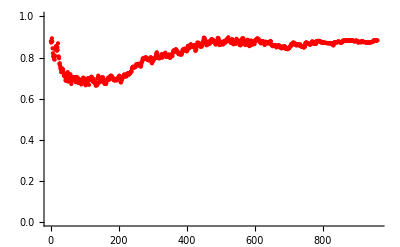

```mathematica
ListPlot[MITN1CondIR75CouNew,PlotRange->{{0,960},{0,1}},PlotStyle->{Red}]
```

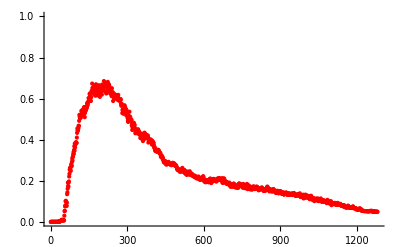

```mathematica
ListPlot[MITMLCondIR89CouNew,PlotRange->{{0,1280},{0,1}},PlotStyle->{Red}]
```

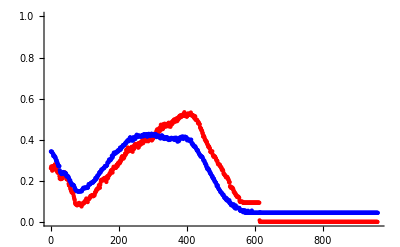

```mathematica
Show[ListPlot[MITMLCondIR75CouNew,PlotRange->{{0,960},{0,1}},PlotStyle->{Red}],ListPlot[MITMLR75New,PlotRange->{{0,960},{0,1}},PlotStyle->{Blue}]]
```

```mathematica
MINorm[200]
```

{0.521458}[200]

```mathematica
MITMRR89=MINorm;
```

```mathematica
MITMRR89Cou=MITMRR89;
```

```mathematica
MITMLR89Cou=MITMLR89;
```

```mathematica
MITMLCondIR89Cou=MINorm;
```

```mathematica
MITN3R89Cou=MINorm;
```

```mathematica
MITN1R75Cou=MINorm;
```

```mathematica
MITN1CondIR75Cou=MINorm;
```

```mathematica
MITN5R89Cou=MINorm;Save["MITN5R89Cou.dat",MITN5R89Cou];
```

```mathematica
Get["MITS2R75.dat"];Get["MITN1R75.dat"];
```

Get::noopen: Cannot open MITS2R75.dat.

Get::noopen: Cannot open MITN1R75.dat.

```mathematica
MITN1R75=MINorm;Save["MITN1R75.dat",MITN1R75];
```

```mathematica
Show[ListPlot[MITN1R75,PlotRange->{{0,400},{0,1}},Axes->True,PlotStyle->{Red}],ListPlot[MITS2R75,PlotRange->{{0,400},{0,1}},Axes->True,PlotStyle->{Red}],AxesLabel->{"time","MI"}]
```

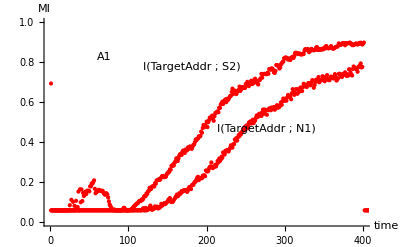

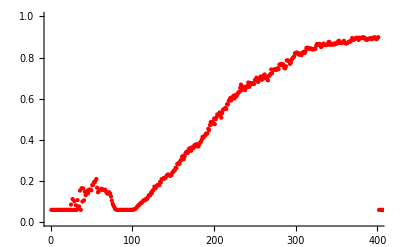

```mathematica
ListPlot[MITS2R75,PlotRange->{{0,400},{0,1}},Axes->True,PlotStyle->{Red}]
```

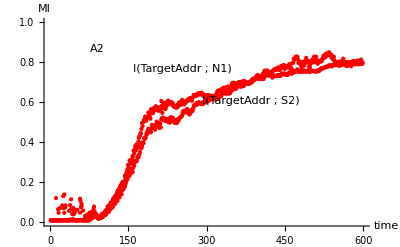

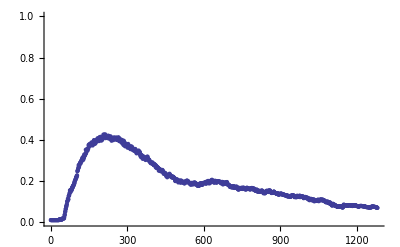

```mathematica
ListPlot[MITMLR89,PlotRange->{{0,1280},{0,1}},Axes->True]
```

```mathematica
MITS2R75[[200]]
```

0.503064

```mathematica
CompVar
```

```mathematica
MINormSandR=MINorm
```

```mathematica
MITCR75=MITCA75;
```

```mathematica
MITCcondIR75=MITCcondIA75;
```

```mathematica
MITN1R75=MITN1A75;
```

```mathematica
MITN1condIR75=MITN1condIA75;
```

```mathematica
Save["MITN1condIR75.dat",MITN1condIR75];
Save["MITN1R75.dat",MITN1R75];
```

```mathematica
Save["MITS2R75.dat",MITS2R75];
```

```mathematica
Save["MITN1R89.dat",MITN1R89];
```

```mathematica
Save["MITN1CondIR89.dat",MITN1CondIR89];
```

```mathematica
Save["MITMRR89Cou.dat",MITMRR89Cou];
Save["MITMLR89Cou.dat",MITMLR89Cou];
Save["MITMLCondIR89Cou.dat",MITMLCondIR89Cou];
```

```mathematica
Save["MITN1R75Cou.dat",MITN1R75Cou];
```

```mathematica
Save["MITN3R89Cou.dat",MITN3R89Cou];
```

```mathematica
Get["MITCcondIA75Copy.dat"]
```

```mathematica
Clear[MITCcondIA75Copy]
```

```mathematica
zeros=ConstantArray[0,98]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[MINorm]
```

501

```mathematica
Length[zeros]
```

98

```mathematica
Length[MITN1CondIR89]
```

599

```mathematica
MITN1CondIR89=MINorm;
```

```mathematica
MITN1CondIR89=Join[zeros,MINorm];
```

```mathematica
Max[MINorm]
```

0.794551

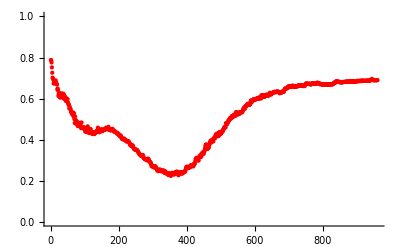

```mathematica
p1=ListPlot[MITN1R75Cou,PlotRange->{{0,960},{0,1}},Axes->True,PlotStyle->{Red}]
```

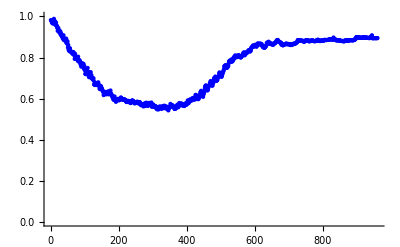

```mathematica
p2=ListPlot[MITN1CondIR75Cou,PlotRange->{{0,960},{0,1}},Axes->True,PlotStyle->{Blue}]
```

```mathematica
Show[p1,p2,AxesLabel->{"time","MI"}]
```

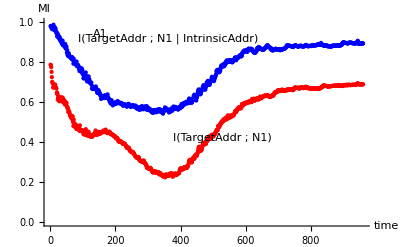

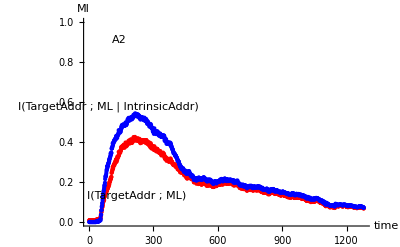

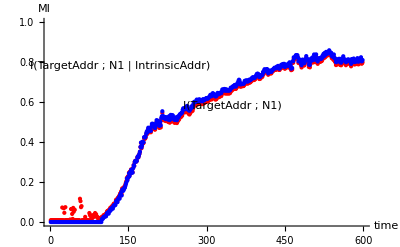

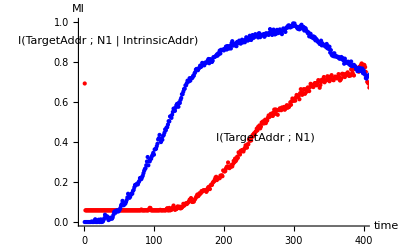

1600

-2.75897×10^-17

Fri 16 Dec 2011 13:48:42

```mathematica
MI
```

0.593395

```mathematica
(*** Estimating Conditional Mutual Information ***)(** Final, working, reported project version **)
DateString[]
Comp="ML";
EndTime=PreTrial/0.1;
MINorm={};IntrinsicTargetVar={};TargetVar={};
For[rec=1,rec≤NumRecordings,rec++,
	TrialData=RecordingFiles[[rec]];
	target=TrialData[[1]][[1]];
	TargetVar=Append[TargetVar,target];
	TrialData=RecordingFilesROnly[[rec]];
	LastRow=TrialData[[TrialLogSize]];
	CompPos=Position[Components,"X"][[1]][[1]];
	intrinsicTarget=LastRow[[AgentRecordingLength+CompPos]];
	IntrinsicTargetVar=Append[IntrinsicTargetVar,intrinsicTarget];
];
targetbins=Table[i,{i,firstTarget,lastTarget+targetBinSize,targetBinSize}];
intrinsicbins=Table[i,{i,0.0,WorldLength+intrinsicBinSize,intrinsicBinSize}];
intrinsicTargetVariates=Thread[{IntrinsicTargetVar,TargetVar}];
ITbincounts=BinCounts[intrinsicTargetVariates,{0.0,WorldLength+intrinsicBinSize,intrinsicBinSize},
												{firstTarget,lastTarget+targetBinSize,targetBinSize}];
targetvals=Table[i,{i,firstTarget,lastTarget,targetBinSize}];
intrinsicvals=Table[i,{i,0.0,WorldLength,intrinsicBinSize}];
intrinstargets=Table[{x,y},{x,intrinsicvals},{y,targetvals}];
fintrinstargets=Flatten[intrinstargets,1];
fITbincounts=Flatten[ITbincounts,1];
ITcofreqs=Thread[{fintrinstargets,fITbincounts}];
pIntrinsicTarget=Interpolation[ITcofreqs,InterpolationOrder->2];
sumpIntrinsicTarget=Sum[pIntrinsicTarget[x,y],{x,intrinsicvals},{y,targetvals}];

Ibincounts = BinCounts[IntrinsicTargetVar,{0.0,WorldLength+intrinsicBinSize,intrinsicBinSize}];
fIbincounts=Flatten[Ibincounts,2];
Ifreqs=Thread[{intrinsicvals,fIbincounts}];
pIntrinsic=Interpolation[Ifreqs,InterpolationOrder->2];
sumpIntrinsic=Sum[pIntrinsic[x],{x,intrinsicvals}];

EntropyTcondI=0.0;
For[i=0,i≤WorldLength,i+=intrinsicBinSize,
For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
	pit=pIntrinsicTarget[i,t]/sumpIntrinsicTarget;
	pi=pIntrinsic[i]/sumpIntrinsic;
	If[pit<10^-7,pit=0.0];
	If[pi<10^-7,pi=0.0];
	If[pit==0.0,
		EntropyTcondI-=0.0,
		EntropyTcondI-=pit*Log[2,pit/pi]
	];
];
];

For[time=800,time≤800,time++,
	Print[time];
	CompVar={};
	For[rec=1,rec≤NumRecordings,rec++,
		TrialData=RecordingFiles[[rec]];
		TimedRow=TrialData[[time]];
		CompPos=Position[Components,Comp][[1]][[1]];
		If[Agent=="R",
			CompValue=TimedRow[[AgentRecordingLength+CompPos]],
			CompValue=TimedRow[[CompPos]]
		];
		CompVar=Append[CompVar,CompValue];
	];
	
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	IntrinsicCompVariates=Thread[{IntrinsicTargetVar,CompVar}];
	ICTvariates=Thread[{IntrinsicTargetVar,CompVar,TargetVar}];
	ICbincounts=BinCounts[IntrinsicCompVariates,{0.0,WorldLength+intrinsicBinSize,intrinsicBinSize},{0.0,1.0+compBinSize,compBinSize}];
	ICTbincounts=BinCounts[ICTvariates,{0.0,WorldLength+intrinsicBinSize,intrinsicBinSize},{0.0,1.0+compBinSize,compBinSize},
												{firstTarget,lastTarget+targetBinSize,targetBinSize}];
	compvals=Table[i,{i,0.0,1.0,compBinSize}];
	intrinscomps=Table[{x,y},{x,intrinsicvals},{y,compvals}];
	ICTs=Table[{x,y,z},{x,intrinsicvals},{y,compvals},{z,targetvals}];
	fintrinscomps=Flatten[intrinscomps,1];
	fICTs=Flatten[ICTs,2];
	fICbincounts=Flatten[ICbincounts,1];
	fICTbincounts=Flatten[ICTbincounts,2];
	ICcofreqs=Thread[{fintrinscomps,fICbincounts}];
	ICTcofreqs=Thread[{fICTs,fICTbincounts}];
	pIntrinsicComp=Interpolation[ICcofreqs,InterpolationOrder->2];
	pICT=Interpolation[ICTcofreqs,InterpolationOrder->2];
	sumpIntrinsicComp=Sum[pIntrinsicComp[x,y],{x,intrinsicvals},{y,compvals}];
	sumpICT=Sum[pICT[x,y,z],{x,intrinsicvals},{y,compvals},{z,targetvals}];

	Entr=0.0;
	For[i=0,i≤WorldLength,i+=intrinsicBinSize,
	For[c=0.0,c≤1.0,c+=compBinSize,
	For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
		pict=pICT[i,c,t]/sumpICT;
		pic=pIntrinsicComp[i,c]/sumpIntrinsicComp;
		pit=pIntrinsicTarget[i,t]/sumpIntrinsicTarget;
		pi=pIntrinsic[i]/sumpIntrinsic;
		If[pict<10^-7,pict=0.0];
		If[pit<10^-7,pit=0.0];
		If[pic<10^-7,pic=0.0];
		If[pi<10^-7,pi=0.0];
		If [pict==0.0||pic==0.0||pit==0.0 || pi==0.0,
			Entr+=0.0,
			v=Log[2,(pict*pi)/(pit*pic)];
			If[v==Infinity,
				Print[v];Entr+=0.0, 
				Entr+=pict*v;
			];
		];
	];
	];
	];
	MI=Entr/EntropyTcondI;
	MINorm=Append[MINorm,MI];
	Print[MI];
];
DateString[]
```

Sat 3 Mar 2012 18:54:16

800

0.514565

Sat 3 Mar 2012 18:54:20

```mathematica
(*** Estimating Conditional Mutual Information ***) (** Older version **)
DateString[]
Comp="S2";
EndTime=PreTrial/0.1;
MINorm={};DistanceVar={};TargetVar={};
For[rec=1,rec≤NumRecordings,rec++,
	TrialData=RecordingFiles[[rec]];
	target=TrialData[[1]][[1]];
	TargetVar=Append[TargetVar,target];
	distance=TrialData[[1]][[2]];
	DistanceVar=Append[DistanceVar,distance];
];
targetbins=Table[i,{i,firstTarget,lastTarget+targetBinSize,targetBinSize}];
distancebins=Table[i,{i,0.0,(WorldLength/2)+distanceBinSize,distanceBinSize}];
distanceTargetVariates=Thread[{DistanceVar,TargetVar}];
DTbincounts=BinCounts[distanceTargetVariates,{0.0,(WorldLength/2)+distanceBinSize,distanceBinSize},
												{firstTarget,lastTarget+targetBinSize,targetBinSize}];
targetvals=Table[i,{i,firstTarget,lastTarget,targetBinSize}];
distancevals=Table[i,{i,0.0,WorldLength/2,distanceBinSize}];
diststargets=Table[{x,y},{x,distancevals},{y,targetvals}];
fdiststargets=Flatten[diststargets,1];
fDTbincounts=Flatten[DTbincounts,1];
DTcofreqs=Thread[{fdiststargets,fDTbincounts}];
pDistanceTarget=Interpolation[DTcofreqs,InterpolationOrder->2];
sumpDistanceTarget=Sum[pDistanceTarget[x,y],{x,distancevals},{y,targetvals}];
EntropyDcondT=0.0;
pt=1/Length[targetvals];
For[d=0,d≤WorldLength/2,d+=distanceBinSize,
For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
	pdt=pDistanceTarget[d,t]/sumpDistanceTarget;
	If[pdt<10^-7,pdt=0.0];
	If[pdt==0.0,
		EntropyDcondT-=0.0,
		EntropyDcondT-=pdt*Log[2,pdt/pt]
	];
];
];

For[time=250,time≤250,time++,
	Print[time];
	CompVar={};
	For[rec=1,rec≤NumRecordings,rec++,
		TrialData=RecordingFiles[[rec]];
		TimedRow=TrialData[[time]];
		CompPos=Position[Components,Comp][[1]][[1]];
		(*CompValue=TimedRow[[AgentRecordingLength+CompPos]];*)
		CompValue=TimedRow[[CompPos]];
		CompVar=Append[CompVar,CompValue];
	];
	
	compbins=Table[i,{i,0.0,1.0+compBinSize,compBinSize}];
	targetCompVariates=Thread[{TargetVar,CompVar}];
	DCTvariates=Thread[{DistanceVar,CompVar,TargetVar}];
	TCbincounts=BinCounts[targetCompVariates,{firstTarget,lastTarget+targetBinSize,targetBinSize},{0.0,1.0+compBinSize,compBinSize}];
	DCTbincounts=BinCounts[DCTvariates,{0.0,(WorldLength/2)+distanceBinSize,distanceBinSize},{0.0,1.0+compBinSize,compBinSize},
												{firstTarget,lastTarget+targetBinSize,targetBinSize}];
	compvals=Table[i,{i,0.0,1.0,compBinSize}];
	targetscomps=Table[{x,y},{x,targetvals},{y,compvals}];
	DCTs=Table[{x,y,z},{x,distancevals},{y,compvals},{z,targetvals}];
	ftargetscomps=Flatten[targetscomps,1];
	fDCTs=Flatten[DCTs,2];
	fTCbincounts=Flatten[TCbincounts,1];
	fDCTbincounts=Flatten[DCTbincounts,2];
	TCcofreqs=Thread[{ftargetscomps,fTCbincounts}];
	DCTcofreqs=Thread[{fDCTs,fDCTbincounts}];
	pTargetComp=Interpolation[TCcofreqs,InterpolationOrder->2];
	pDCT=Interpolation[DCTcofreqs,InterpolationOrder->2];
	sumpTargetComp=Sum[pTargetComp[x,y],{x,targetvals},{y,compvals}];
	sumpDCT=Sum[pDCT[x,y,z],{x,distancevals},{y,compvals},{z,targetvals}];

	Entr=0.0;
	For[d=0,d≤WorldLength/2,d+=distanceBinSize,
	For[c=0.0,c≤1.0,c+=compBinSize,
	For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
		pdct=pDCT[d,c,t]/sumpDCT;
		ptc=pTargetComp[t,c]/sumpTargetComp;
		pdt=pDistanceTarget[d,t]/sumpDistanceTarget;
		If[pdct<10^-7,pdct=0.0];
		If[pdt<10^-7,pdt=0.0];
		If[ptc<10^-7,ptc=0.0];
		If [pdct==0.0||ptc==0.0||pdt==0.0,
			Entr+=0.0,
			v=Log[2,(pdct*pt)/(pdt*ptc)];
			If[v==Infinity,
				Print[ptc,v];Entr+=0.0, 
				Entr+=pdct*v;
			];
		];
	];
	];
	];
	MI=Entr/EntropyDcondT;
	MINorm=Append[MINorm,MI];
];
DateString[]
```

Thu 15 Dec 2011 03:41:12

250

Thu 15 Dec 2011 03:41:16

```mathematica
ListPlot[MINorm,PlotRange->{{0,600},{0,1}},Axes->True]
```

```mathematica
MI
```

0.041056

```mathematica
Entr
```

2.61411

```mathematica
MI
```

0.747332

```mathematica
EntropyDcondT=0.0;
pt=1/Length[targetvals];
For[d=0,d≤WorldLength/2,d+=distanceBinSize,
For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
	pdt=pDistanceTarget[d,t]/sumpDistanceTarget;
	If[pdt<10^-7,pdt=0.0];
	If[pdt==0.0,
		EntropyDcondT-=0.0,
		EntropyDcondT-=pdt*Log[2,pdt/pt]
	];
];
];
```

```mathematica
EntropyDcondT
```

3.39793

```mathematica
Entr
```

-1.45066

```mathematica
a=Table[i,{i,1,3,1}]
```

{1,2,3}

```mathematica
b=Table[i,{i,4,6,1}]
```

{4,5,6}

```mathematica
c=Table[i,{i,7,9,1}]
```

{7,8,9}

```mathematica
abc=Table[{x,y,z},{x,a},{y,b},{z,c}]
```

{{{{1,4,7},{1,4,8},{1,4,9}},{{1,5,7},{1,5,8},{1,5,9}},{{1,6,7},{1,6,8},{1,6,9}}},{{{2,4,7},{2,4,8},{2,4,9}},{{2,5,7},{2,5,8},{2,5,9}},{{2,6,7},{2,6,8},{2,6,9}}},{{{3,4,7},{3,4,8},{3,4,9}},{{3,5,7},{3,5,8},{3,5,9}},{{3,6,7},{3,6,8},{3,6,9}}}}

```mathematica
Flatten[abc,2]
```

{{1,4,7},{1,4,8},{1,4,9},{1,5,7},{1,5,8},{1,5,9},{1,6,7},{1,6,8},{1,6,9},{2,4,7},{2,4,8},{2,4,9},{2,5,7},{2,5,8},{2,5,9},{2,6,7},{2,6,8},{2,6,9},{3,4,7},{3,4,8},{3,4,9},{3,5,7},{3,5,8},{3,5,9},{3,6,7},{3,6,8},{3,6,9}}

```mathematica
Distbincounts = BinCounts[DistanceVar,{0.0,(WorldLength/2)+distanceBinSize,distanceBinSize}];
fDistbincounts=Flatten[Distbincounts,2];
Dfreqs=Thread[{distancevals,fDistbincounts}];
pDistance=Interpolation[Dfreqs,InterpolationOrder->2];
sumpDistance=Sum[pDistance[x],{x,distancevals}];
distanceEntropy=0.0;
For[dist=0,dist≤WorldLength/2,dist+=distanceBinSize,
	pd=pDistance[dist]/sumpDistance;
	If[pd<10^-7,pd=0.0];
	If[pd==0.0,
		distanceEntropy-=0.0,
		distanceEntropy-=pd*Log[2,pd];
	];
];
```

```mathematica
distanceEntropy
```

5.20885

```mathematica
pDistance[0]
```

0.

```mathematica
BinCounts[DistanceVar,{0.0,(WorldLength/2)+distanceBinSize,distanceBinSize}]
```

{0,2,6,10,16,20,28,32,38,44,44,54,54,66,64,76,46}

```mathematica
distanceEntropy
```

Indeterminate

```mathematica
targetbins
```

{3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1}

```mathematica
Clear["Global`*"]
```

```mathematica
v
```

-0.485427

```mathematica
pdct
```

0.

```mathematica
MI
```

0.130761-3.84139×10^-14 ⅈ

```mathematica
distancevals=Table[i,{i,0.0,WorldLength/2,distanceBinSize}];
```

```mathematica
t=Table[{x,y,z},{x,distancevals},{y,compvals},{z,targetvals}]
```

{{{{0.,0.,3.},{0.,0.,3.2},{0.,0.,3.4},{0.,0.,3.6},{0.,0.,3.8},{0.,0.,4.},{0.,0.,4.2},{0.,0.,4.4},{0.,0.,4.6},{0.,0.,4.8},{0.,0.,5.},{0.,0.,5.2},{0.,0.,5.4},{0.,0.,5.6},{0.,0.,5.8},{0.,0.,6.},{0.,0.,6.2},{0.,0.,6.4},{0.,0.,6.6},{0.,0.,6.8},{0.,0.,7.}},{{0.,0.01,3.},{0.,0.01,3.2},{0.,0.01,3.4},{0.,0.01,3.6},{0.,0.01,3.8},{0.,0.01,4.},{0.,0.01,4.2},{0.,0.01,4.4},{0.,0.01,4.6},{0.,0.01,4.8},{0.,0.01,5.},{0.,0.01,5.2},{0.,0.01,5.4},{0.,0.01,5.6},{0.,0.01,5.8},{0.,0.01,6.},{0.,0.01,6.2},{0.,0.01,6.4},{0.,0.01,6.6},{0.,0.01,6.8},{0.,0.01,7.}},«98»,{{0.,1.,3.},{0.,1.,3.2},{0.,1.,3.4},{0.,1.,3.6},{0.,1.,3.8},{0.,1.,4.},{0.,1.,4.2},{0.,1.,4.4},{0.,1.,4.6},{0.,1.,4.8},{0.,1.,5.},{0.,1.,5.2},{0.,1.,5.4},{0.,1.,5.6},{0.,1.,5.8},{0.,1.,6.},{0.,1.,6.2},{0.,1.,6.4},{0.,1.,6.6},{0.,1.,6.8},{0.,1.,7.}}},«24»,{{{5.,0.,3.},{5.,0.,3.2},{5.,0.,3.4},{5.,0.,3.6},«14»,{5.,0.,6.6},{5.,0.,6.8},{5.,0.,7.}},«99»,{«1»}}}

```mathematica
Flatten[t,2]
```

{{0.,0.,3.},{0.,0.,3.2},{0.,0.,3.4},{0.,0.,3.6},{0.,0.,3.8},{0.,0.,4.},{0.,0.,4.2},{0.,0.,4.4},{0.,0.,4.6},{0.,0.,4.8},{0.,0.,5.},{0.,0.,5.2},{0.,0.,5.4},{0.,0.,5.6},{0.,0.,5.8},{0.,0.,6.},{0.,0.,6.2},{0.,0.,6.4},{0.,0.,6.6},«55109»,{5.,1.,3.6},{5.,1.,3.8},{5.,1.,4.},{5.,1.,4.2},{5.,1.,4.4},{5.,1.,4.6},{5.,1.,4.8},{5.,1.,5.},{5.,1.,5.2},{5.,1.,5.4},{5.,1.,5.6},{5.,1.,5.8},{5.,1.,6.},{5.,1.,6.2},{5.,1.,6.4},{5.,1.,6.6},{5.,1.,6.8},{5.,1.,7.}}

```mathematica
t2=Table[{x,y},{x,distancevals},{y,targetvals}];
```

```mathematica
Thread[{{1,2},{3,4},{5,6}}]
```

{{1,3,5},{2,4,6}}

```mathematica
distancebins
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2}

```mathematica
targetbins
```

{3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2}

```mathematica
Table[i,{i,0,1,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
Log[2,Length[targetvals]]//N
```

5.35755

```mathematica
MI
```

0.00887694

```mathematica
Length[targetvals]
```

41

```mathematica
targetvals
```

{3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.}

```mathematica
BinLists[biVariates,{{targetbins},{compbins}}]
```

```mathematica
res[[2]]
```

{{{3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1}},{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01}}}

```mathematica
compbins
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01}

```mathematica
BinCounts[{1,3,2,1,4,5,6,2},{1,10,1}]
```

{2,2,1,1,1,1,0,0,0}

```mathematica
BinLists[{1,3,2,1,4,5,6,2}]
```

{{},{1,1},{2,2},{3},{4},{5},{6}}

```mathematica
b=BinCounts[{{3,1},{3,2},{3,1},{3,3}},{1,6,1},{1,5,1}]
```

{{0,0,0,0},{0,0,0,0},{2,1,1,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Flatten[b,1]
```

{0,0,0,0,0,0,0,0,2,1,1,0,0,0,0,0,0,0,0,0}

```mathematica
b2=BinCounts[{{3,1,3},{3,2,3},{3,1,3},{3,3,2}},{1,6,1},{1,5,1},{1,4,1}]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,2},{0,0,1},{0,1,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
Flatten[b2,2]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Reap[Histogram3D[biVariates,{{targetbins},{compbins}},
							Function[{xbins,ybins,counts},Sow[counts]]]]
```

```mathematica
BinCounts[biVariates,{3,7.1,0.1},{0,1.01,0.01}]
```

{{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{40,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Flatten[res,1]
```

{0,0,0,0,0,0,0,0,2,1,1,0,0,0,0,0}

```mathematica
[biVariates]
```

{{0,0},{0,160},{0,120},{0,160},{0,120},{0,40}}

```mathematica
bc[1,1]
```

BinCounts[{{1,1},{1,2},{3,1},{2,3}},{{0,1,2,3,4,5},{0,1,2,3,4,5}}][1,1]

```mathematica
Length[targetvals]
```

41

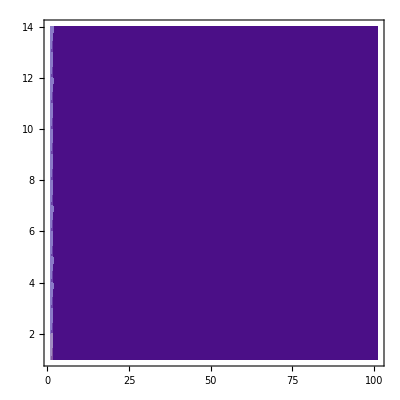

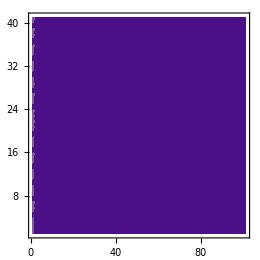

```mathematica
ListDensityPlot[bincounts]
```

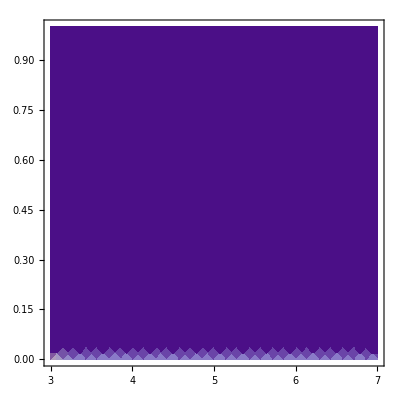

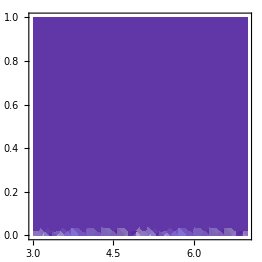

```mathematica
DensityPlot[pTargetComp[x,y],{x,3,7},{y,0,1}]
```

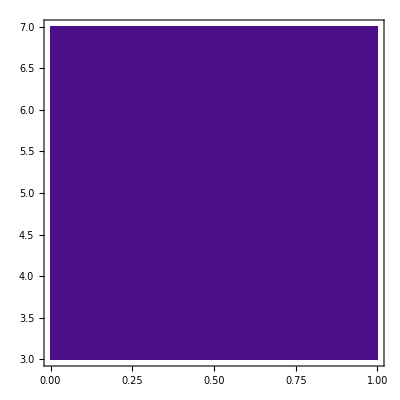

```mathematica
DensityPlot[pDCT[5,y,z],{y,0,1},{z,3,7}]
```

```mathematica
Length[MINorm]
```

431

```mathematica
0.065/(0.047619*0.906667)
```

```mathematica
Log[2,1.505515657900161]
```

0.590258

```mathematica
0.047619*0.906667
```

0.0431746

```mathematica
a=3;
a+=3*4
```

15

```mathematica
Log[2,Length[targetvals]]//N
```

4.39232

```mathematica
0.55/4.39
```

0.125285

```mathematica
count2
```

27.

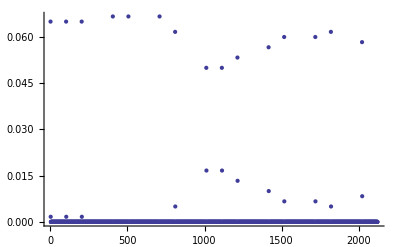

```mathematica
ListPlot[Flatten[Table[pTargetComp[t,c],{t,targetvals},{c,compvals}]]]
```

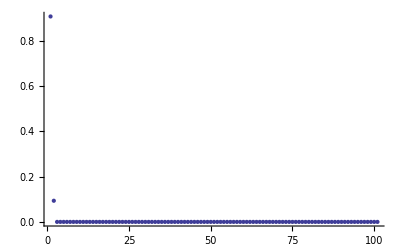

```mathematica
ListPlot[Flatten[Table[pComp[c],{c,compvals}]]]
```

```mathematica
pTargetComp[4,0.0]
```

0.0666667

```mathematica
Length[targetvals]
```

21

```mathematica
ListPlot[Flatten[Table[pComp[c],{c,compvals}]]]
```

```mathematica
tars
```

{3.,3.3,3.6,3.9,4.2,4.5,4.8,5.1,5.4,5.7,6.,6.3,6.6,6.9}

```mathematica
Length[fbincounts]
```

2121

```mathematica
targetbins
```

{3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2}

```mathematica
Length[MINorm]
```

59

```mathematica
SMINormN150To600=MINorm;
```

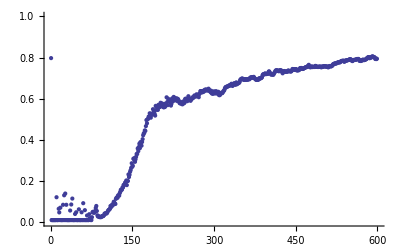

```mathematica
ListPlot[MINorm,PlotRange->{{0,600},{0,1}},Axes->True]
```

```mathematica
a=3;b=4;
If[a<2||a<-4,
	a=2;Print["Yes"],
	If[b<3||b<0,
		b=5;Print["Yes2"],
		b=6;Print["No"]
	];
]
```

No

```mathematica
a
```

4

```mathematica
-8.9*10^-15<10^-7
```

True

```mathematica
10^2
```

100

```mathematica
10^-14//N
```

1.×10^-14

```mathematica
count
```

1316.

```mathematica
time
```

61

```mathematica
count
```

1400.

```mathematica
count2
```

14.

```mathematica
Entr
```

0.

```mathematica
Position[Components,Comp][[1]][[1]]
```

6

```mathematica
Print[ptc]
```

0.

```mathematica
count
```

1260.

```mathematica
Entr
```

0.

```mathematica
c
```

1.01

```mathematica
v
```

3.80735

```mathematica
ptc
```

0.

```mathematica
pc
```

0.

```mathematica
pt
```

0.0714286

```mathematica
sumpComp
```

1.

```mathematica
sumpTargetComp
```

1.

```mathematica
NumRecordings
```

1

```mathematica
pTargetComp[3,0]
```

InterpolatingFunction[{{3.,6.9},{0.,1.}},<>][1][3,0]

```mathematica
Log[2,Length[targetvals]]//N
```

3.80735

```mathematica
compvals
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
Plot[{pTargetComp[x,y]},{{x,3,7},{y,0,1}}]
```

Plot::pllim: Range specification {{x, 3, 7}, {y, 0, 1}} is not of the form {x, xmin, xmax}.

Plot[{pTargetComp[x,y]},{{x,3,7},{y,0,1}}]

```mathematica
pComp[0.1]
```

0.

```mathematica
Log[2,0.00002]
```

-15.6096

```mathematica
sumpComp
```

600.

```mathematica
sumpTargetComp
```

600.

```mathematica
targetvals
```

{3.,3.3,3.6,3.9,4.2,4.5,4.8,5.1,5.4,5.7,6.,6.3,6.6,6.9}

```mathematica
For[t=firstTarget,t≤lastTarget,t+=targetBinSize,
	For[c=0;c≤1,c+=compBinSize,
		ptc=pTargetComp[t,c];
		pt=1/Length[targetvals];
		pc=pComp[c];
		If [ptc==0.0||pt==0.0||pc==0.0,
			Entr+=0.0,
			v=Log[2,ptc/(pt*pc)];
			If[Head[v]==Complex||Head[v]==Indeterminate||Head[v]==Infinity,
				Entr+=0.0, 
				Entr+=ptc*v];
		];
	];
	];
	MI=Entr/Log[2,Length[targetvals]]
```

```mathematica
pTargetComp
```

```mathematica
Sum[pTargetComp[x,y],{x,targetvals},{y,compvals}]
```

1.

```mathematica
MINorm
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Plot[MINorm[[i]],{i,1,59}]
```

Part::pspec: Part specification 1.00118 is neither an integer nor a list of integers.

Part::pspec: Part specification 2.18486 is neither an integer nor a list of integers.

Part::pspec: Part specification 3.36853 is neither an integer nor a list of integers.

General::stop: Further output of Part will be suppressed during this calculation.

-Graphics-

```mathematica
i=0.09381486331732074-7.966265953468043*^-17 ⅈ
```

0.0938149-7.96627×10^-17 ⅈ

```mathematica
i=Indeterminate
```

Indeterminate

```mathematica
i==Indeterminate
```

Indeterminate==Indeterminate

```mathematica
Length[MINorm]
```

59

```mathematica
Entropy
```

Entropy

```mathematica
E
```

ⅇ

```mathematica
Ent
```

Ent

```mathematica
Log[2,10]//N
```

3.32193

```mathematica
pTargetComp[6.9,0.7733]
```

0.

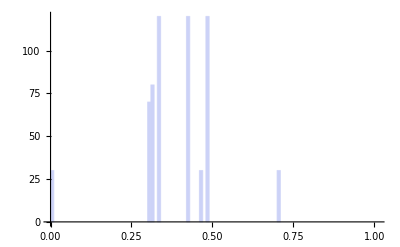
{-Graphics-,{{{30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,70,80,0,120,0,0,0,0,0,0,0,0,120,0,0,0,30,0,120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}}

```mathematica
{plot2,{bincounts2}}=Reap[Histogram[CompVar,{compbins},Function[{bins,counts},Sow[counts]]]]
```

```mathematica
fbincounts2
```

{30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,70,80,0,120,0,0,0,0,0,0,0,0,120,0,0,0,30,0,120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
fbincounts2=fbincounts2/Sum[fbincounts2[[i]],{i,1,Length[fbincounts2]}]//N
```

{0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.116667,0.133333,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.2,0.,0.,0.,0.05,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Sum[fbincounts2[[i]],{i,1,Length[fbincounts2]}]
```

1.

```mathematica
fbincounts2[[1]]
```

30

```mathematica
fbincounts2=Flatten[bincounts2,2];
fbincounts2=fbincounts2/Sum[fbincounts2[[i]],{i,1,Length[fbincounts2]}]//N;
	freqs=Thread[{comps,fbincounts2}];
	pComp=Interpolation[freqs]
```

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
pComp[0]
```

0.05

```mathematica
pComp=pComp/Sum[pComp[x],{x,0,1}]
```

0.0333333 InterpolatingFunction[{{0.,1.}},<>]

```mathematica
pComp[0]
```

(0.0333333 InterpolatingFunction[{{0.,1.}},<>])[0]

```mathematica
Length[bincounts2]
```

1

```mathematica
Flatten[bincounts2,2]
```

{30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,70,80,0,120,0,0,0,0,0,0,0,0,120,0,0,0,30,0,120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,30,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
comps
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
compbins
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01}

```mathematica
targetbins
```

{3.,3.3,3.6,3.9,4.2,4.5,4.8,5.1,5.4,5.7,6.,6.3,6.6,6.9,7.2}

```mathematica
f
```

InterpolatingFunction[{{3.,6.9},{0.,1.}},<>]

```mathematica
DateString[]
```

Sun 11 Dec 2011 16:12:46

```mathematica
Histogram3D[biVariates,{{targetbins},{compbins}}]
```

-Graphics3D-

```mathematica
Flatten[bincounts,2]
```

{4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,20,0,0,16,0,0,0,0,0,0,0,0,16,0,0,0,4,0,16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,8,0,0,0,0,0,0,0,0,8,0,0,0,2,0,8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
targetbins
```

{3.,3.3,3.6,3.9,4.2,4.5,4.8,5.1,5.4,5.7,6.,6.3,6.6,6.9,7.2,7.5}

```mathematica
compbins
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01,1.02}

```mathematica
Table[{{x,y},GCD[x,y]},{x,20},{y,20}]
```

{{{{1,1},1},{{1,2},1},{{1,3},1},{{1,4},1},{{1,5},1},{{1,6},1},{{1,7},1},{{1,8},1},{{1,9},1},{{1,10},1},{{1,11},1},{{1,12},1},{{1,13},1},{{1,14},1},{{1,15},1},{{1,16},1},{{1,17},1},{{1,18},1},{{1,19},1},{{1,20},1}},{{{2,1},1},{{2,2},2},{{2,3},1},{{2,4},2},{{2,5},1},{{2,6},2},{{2,7},1},{{2,8},2},{{2,9},1},{{2,10},2},{{2,11},1},{{2,12},2},{{2,13},1},{{2,14},2},{{2,15},1},{{2,16},2},{{2,17},1},{{2,18},2},{{2,19},1},{{2,20},2}},{{{3,1},1},{{3,2},1},{{3,3},3},{{3,4},1},{{3,5},1},{{3,6},3},{{3,7},1},{{3,8},1},{{3,9},3},{{3,10},1},{{3,11},1},{{3,12},3},{{3,13},1},{{3,14},1},{{3,15},3},{{3,16},1},{{3,17},1},{{3,18},3},{{3,19},1},{{3,20},1}},{{{4,1},1},{{4,2},2},{{4,3},1},{{4,4},4},{{4,5},1},{{4,6},2},{{4,7},1},{{4,8},4},{{4,9},1},{{4,10},2},{{4,11},1},{{4,12},4},{{4,13},1},{{4,14},2},{{4,15},1},{{4,16},4},{{4,17},1},{{4,18},2},{{4,19},1},{{4,20},4}},{{{5,1},1},{{5,2},1},{{5,3},1},{{5,4},1},{{5,5},5},{{5,6},1},{{5,7},1},{{5,8},1},{{5,9},1},{{5,10},5},{{5,11},1},{{5,12},1},{{5,13},1},{{5,14},1},{{5,15},5},{{5,16},1},{{5,17},1},{{5,18},1},{{5,19},1},{{5,20},5}},{{{6,1},1},{{6,2},2},{{6,3},3},{{6,4},2},{{6,5},1},{{6,6},6},{{6,7},1},{{6,8},2},{{6,9},3},{{6,10},2},{{6,11},1},{{6,12},6},{{6,13},1},{{6,14},2},{{6,15},3},{{6,16},2},{{6,17},1},{{6,18},6},{{6,19},1},{{6,20},2}},{{{7,1},1},{{7,2},1},{{7,3},1},{{7,4},1},{{7,5},1},{{7,6},1},{{7,7},7},{{7,8},1},{{7,9},1},{{7,10},1},{{7,11},1},{{7,12},1},{{7,13},1},{{7,14},7},{{7,15},1},{{7,16},1},{{7,17},1},{{7,18},1},{{7,19},1},{{7,20},1}},{{{8,1},1},{{8,2},2},{{8,3},1},{{8,4},4},{{8,5},1},{{8,6},2},{{8,7},1},{{8,8},8},{{8,9},1},{{8,10},2},{{8,11},1},{{8,12},4},{{8,13},1},{{8,14},2},{{8,15},1},{{8,16},8},{{8,17},1},{{8,18},2},{{8,19},1},{{8,20},4}},{{{9,1},1},{{9,2},1},{{9,3},3},{{9,4},1},{{9,5},1},{{9,6},3},{{9,7},1},{{9,8},1},{{9,9},9},{{9,10},1},{{9,11},1},{{9,12},3},{{9,13},1},{{9,14},1},{{9,15},3},{{9,16},1},{{9,17},1},{{9,18},9},{{9,19},1},{{9,20},1}},{{{10,1},1},{{10,2},2},{{10,3},1},{{10,4},2},{{10,5},5},{{10,6},2},{{10,7},1},{{10,8},2},{{10,9},1},{{10,10},10},{{10,11},1},{{10,12},2},{{10,13},1},{{10,14},2},{{10,15},5},{{10,16},2},{{10,17},1},{{10,18},2},{{10,19},1},{{10,20},10}},{{{11,1},1},{{11,2},1},{{11,3},1},{{11,4},1},{{11,5},1},{{11,6},1},{{11,7},1},{{11,8},1},{{11,9},1},{{11,10},1},{{11,11},11},{{11,12},1},{{11,13},1},{{11,14},1},{{11,15},1},{{11,16},1},{{11,17},1},{{11,18},1},{{11,19},1},{{11,20},1}},{{{12,1},1},{{12,2},2},{{12,3},3},{{12,4},4},{{12,5},1},{{12,6},6},{{12,7},1},{{12,8},4},{{12,9},3},{{12,10},2},{{12,11},1},{{12,12},12},{{12,13},1},{{12,14},2},{{12,15},3},{{12,16},4},{{12,17},1},{{12,18},6},{{12,19},1},{{12,20},4}},{{{13,1},1},{{13,2},1},{{13,3},1},{{13,4},1},{{13,5},1},{{13,6},1},{{13,7},1},{{13,8},1},{{13,9},1},{{13,10},1},{{13,11},1},{{13,12},1},{{13,13},13},{{13,14},1},{{13,15},1},{{13,16},1},{{13,17},1},{{13,18},1},{{13,19},1},{{13,20},1}},{{{14,1},1},{{14,2},2},{{14,3},1},{{14,4},2},{{14,5},1},{{14,6},2},{{14,7},7},{{14,8},2},{{14,9},1},{{14,10},2},{{14,11},1},{{14,12},2},{{14,13},1},{{14,14},14},{{14,15},1},{{14,16},2},{{14,17},1},{{14,18},2},{{14,19},1},{{14,20},2}},{{{15,1},1},{{15,2},1},{{15,3},3},{{15,4},1},{{15,5},5},{{15,6},3},{{15,7},1},{{15,8},1},{{15,9},3},{{15,10},5},{{15,11},1},{{15,12},3},{{15,13},1},{{15,14},1},{{15,15},15},{{15,16},1},{{15,17},1},{{15,18},3},{{15,19},1},{{15,20},5}},{{{16,1},1},{{16,2},2},{{16,3},1},{{16,4},4},{{16,5},1},{{16,6},2},{{16,7},1},{{16,8},8},{{16,9},1},{{16,10},2},{{16,11},1},{{16,12},4},{{16,13},1},{{16,14},2},{{16,15},1},{{16,16},16},{{16,17},1},{{16,18},2},{{16,19},1},{{16,20},4}},{{{17,1},1},{{17,2},1},{{17,3},1},{{17,4},1},{{17,5},1},{{17,6},1},{{17,7},1},{{17,8},1},{{17,9},1},{{17,10},1},{{17,11},1},{{17,12},1},{{17,13},1},{{17,14},1},{{17,15},1},{{17,16},1},{{17,17},17},{{17,18},1},{{17,19},1},{{17,20},1}},{{{18,1},1},{{18,2},2},{{18,3},3},{{18,4},2},{{18,5},1},{{18,6},6},{{18,7},1},{{18,8},2},{{18,9},9},{{18,10},2},{{18,11},1},{{18,12},6},{{18,13},1},{{18,14},2},{{18,15},3},{{18,16},2},{{18,17},1},{{18,18},18},{{18,19},1},{{18,20},2}},{{{19,1},1},{{19,2},1},{{19,3},1},{{19,4},1},{{19,5},1},{{19,6},1},{{19,7},1},{{19,8},1},{{19,9},1},{{19,10},1},{{19,11},1},{{19,12},1},{{19,13},1},{{19,14},1},{{19,15},1},{{19,16},1},{{19,17},1},{{19,18},1},{{19,19},19},{{19,20},1}},{{{20,1},1},{{20,2},2},{{20,3},1},{{20,4},4},{{20,5},5},{{20,6},2},{{20,7},1},{{20,8},4},{{20,9},1},{{20,10},10},{{20,11},1},{{20,12},4},{{20,13},1},{{20,14},2},{{20,15},5},{{20,16},4},{{20,17},1},{{20,18},2},{{20,19},1},{{20,20},20}}}

```mathematica
Flatten[Table[{{x,y},GCD[x,y]},{x,20},{y,20}],1]
```

{{{1,1},1},{{1,2},1},{{1,3},1},{{1,4},1},{{1,5},1},{{1,6},1},{{1,7},1},{{1,8},1},{{1,9},1},{{1,10},1},{{1,11},1},{{1,12},1},{{1,13},1},{{1,14},1},{{1,15},1},{{1,16},1},{{1,17},1},{{1,18},1},{{1,19},1},{{1,20},1},{{2,1},1},{{2,2},2},{{2,3},1},{{2,4},2},{{2,5},1},{{2,6},2},{{2,7},1},{{2,8},2},{{2,9},1},{{2,10},2},{{2,11},1},{{2,12},2},{{2,13},1},{{2,14},2},{{2,15},1},{{2,16},2},{{2,17},1},{{2,18},2},{{2,19},1},{{2,20},2},{{3,1},1},{{3,2},1},{{3,3},3},{{3,4},1},{{3,5},1},{{3,6},3},{{3,7},1},{{3,8},1},{{3,9},3},{{3,10},1},{{3,11},1},{{3,12},3},{{3,13},1},{{3,14},1},{{3,15},3},{{3,16},1},{{3,17},1},{{3,18},3},{{3,19},1},{{3,20},1},{{4,1},1},{{4,2},2},{{4,3},1},{{4,4},4},{{4,5},1},{{4,6},2},{{4,7},1},{{4,8},4},{{4,9},1},{{4,10},2},{{4,11},1},{{4,12},4},{{4,13},1},{{4,14},2},{{4,15},1},{{4,16},4},{{4,17},1},{{4,18},2},{{4,19},1},{{4,20},4},{{5,1},1},{{5,2},1},{{5,3},1},{{5,4},1},{{5,5},5},{{5,6},1},{{5,7},1},{{5,8},1},{{5,9},1},{{5,10},5},{{5,11},1},{{5,12},1},{{5,13},1},{{5,14},1},{{5,15},5},{{5,16},1},{{5,17},1},{{5,18},1},{{5,19},1},{{5,20},5},{{6,1},1},{{6,2},2},{{6,3},3},{{6,4},2},{{6,5},1},{{6,6},6},{{6,7},1},{{6,8},2},{{6,9},3},{{6,10},2},{{6,11},1},{{6,12},6},{{6,13},1},{{6,14},2},{{6,15},3},{{6,16},2},{{6,17},1},{{6,18},6},{{6,19},1},{{6,20},2},{{7,1},1},{{7,2},1},{{7,3},1},{{7,4},1},{{7,5},1},{{7,6},1},{{7,7},7},{{7,8},1},{{7,9},1},{{7,10},1},{{7,11},1},{{7,12},1},{{7,13},1},{{7,14},7},{{7,15},1},{{7,16},1},{{7,17},1},{{7,18},1},{{7,19},1},{{7,20},1},{{8,1},1},{{8,2},2},{{8,3},1},{{8,4},4},{{8,5},1},{{8,6},2},{{8,7},1},{{8,8},8},{{8,9},1},{{8,10},2},{{8,11},1},{{8,12},4},{{8,13},1},{{8,14},2},{{8,15},1},{{8,16},8},{{8,17},1},{{8,18},2},{{8,19},1},{{8,20},4},{{9,1},1},{{9,2},1},{{9,3},3},{{9,4},1},{{9,5},1},{{9,6},3},{{9,7},1},{{9,8},1},{{9,9},9},{{9,10},1},{{9,11},1},{{9,12},3},{{9,13},1},{{9,14},1},{{9,15},3},{{9,16},1},{{9,17},1},{{9,18},9},{{9,19},1},{{9,20},1},{{10,1},1},{{10,2},2},{{10,3},1},{{10,4},2},{{10,5},5},{{10,6},2},{{10,7},1},{{10,8},2},{{10,9},1},{{10,10},10},{{10,11},1},{{10,12},2},{{10,13},1},{{10,14},2},{{10,15},5},{{10,16},2},{{10,17},1},{{10,18},2},{{10,19},1},{{10,20},10},{{11,1},1},{{11,2},1},{{11,3},1},{{11,4},1},{{11,5},1},{{11,6},1},{{11,7},1},{{11,8},1},{{11,9},1},{{11,10},1},{{11,11},11},{{11,12},1},{{11,13},1},{{11,14},1},{{11,15},1},{{11,16},1},{{11,17},1},{{11,18},1},{{11,19},1},{{11,20},1},{{12,1},1},{{12,2},2},{{12,3},3},{{12,4},4},{{12,5},1},{{12,6},6},{{12,7},1},{{12,8},4},{{12,9},3},{{12,10},2},{{12,11},1},{{12,12},12},{{12,13},1},{{12,14},2},{{12,15},3},{{12,16},4},{{12,17},1},{{12,18},6},{{12,19},1},{{12,20},4},{{13,1},1},{{13,2},1},{{13,3},1},{{13,4},1},{{13,5},1},{{13,6},1},{{13,7},1},{{13,8},1},{{13,9},1},{{13,10},1},{{13,11},1},{{13,12},1},{{13,13},13},{{13,14},1},{{13,15},1},{{13,16},1},{{13,17},1},{{13,18},1},{{13,19},1},{{13,20},1},{{14,1},1},{{14,2},2},{{14,3},1},{{14,4},2},{{14,5},1},{{14,6},2},{{14,7},7},{{14,8},2},{{14,9},1},{{14,10},2},{{14,11},1},{{14,12},2},{{14,13},1},{{14,14},14},{{14,15},1},{{14,16},2},{{14,17},1},{{14,18},2},{{14,19},1},{{14,20},2},{{15,1},1},{{15,2},1},{{15,3},3},{{15,4},1},{{15,5},5},{{15,6},3},{{15,7},1},{{15,8},1},{{15,9},3},{{15,10},5},{{15,11},1},{{15,12},3},{{15,13},1},{{15,14},1},{{15,15},15},{{15,16},1},{{15,17},1},{{15,18},3},{{15,19},1},{{15,20},5},{{16,1},1},{{16,2},2},{{16,3},1},{{16,4},4},{{16,5},1},{{16,6},2},{{16,7},1},{{16,8},8},{{16,9},1},{{16,10},2},{{16,11},1},{{16,12},4},{{16,13},1},{{16,14},2},{{16,15},1},{{16,16},16},{{16,17},1},{{16,18},2},{{16,19},1},{{16,20},4},{{17,1},1},{{17,2},1},{{17,3},1},{{17,4},1},{{17,5},1},{{17,6},1},{{17,7},1},{{17,8},1},{{17,9},1},{{17,10},1},{{17,11},1},{{17,12},1},{{17,13},1},{{17,14},1},{{17,15},1},{{17,16},1},{{17,17},17},{{17,18},1},{{17,19},1},{{17,20},1},{{18,1},1},{{18,2},2},{{18,3},3},{{18,4},2},{{18,5},1},{{18,6},6},{{18,7},1},{{18,8},2},{{18,9},9},{{18,10},2},{{18,11},1},{{18,12},6},{{18,13},1},{{18,14},2},{{18,15},3},{{18,16},2},{{18,17},1},{{18,18},18},{{18,19},1},{{18,20},2},{{19,1},1},{{19,2},1},{{19,3},1},{{19,4},1},{{19,5},1},{{19,6},1},{{19,7},1},{{19,8},1},{{19,9},1},{{19,10},1},{{19,11},1},{{19,12},1},{{19,13},1},{{19,14},1},{{19,15},1},{{19,16},1},{{19,17},1},{{19,18},1},{{19,19},19},{{19,20},1},{{20,1},1},{{20,2},2},{{20,3},1},{{20,4},4},{{20,5},5},{{20,6},2},{{20,7},1},{{20,8},4},{{20,9},1},{{20,10},10},{{20,11},1},{{20,12},4},{{20,13},1},{{20,14},2},{{20,15},5},{{20,16},4},{{20,17},1},{{20,18},2},{{20,19},1},{{20,20},20}}

```mathematica
targetbins
```

targetbins

```mathematica
Table[i,{i,firstTarget,lastTarget+(2*targetBinSize),targetBinSize}]
```

{3.,3.3,3.6,3.9,4.2,4.5,4.8,5.1,5.4,5.7,6.,6.3,6.6,6.9,7.2,7.5}

```mathematica
Table[i,{i,0,5,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.}

```mathematica
tarscomps=Table[{x,y},{x,tars},{y,comps}];
```

```mathematica
ftarscomps=Flatten[tarscomps,1];
```

```mathematica
fbincounts=Flatten[bincounts,2];
```

```mathematica
ftarscomps
```

{{3.,0.},{3.,0.01},{3.,0.02},{3.,0.03},{3.,0.04},{3.,0.05},{3.,0.06},{3.,0.07},{3.,0.08},{3.,0.09},{3.,0.1},{3.,0.11},{3.,0.12},{3.,0.13},{3.,0.14},{3.,0.15},{3.,0.16},{3.,0.17},{3.,0.18},{3.,0.19},{3.,0.2},{3.,0.21},{3.,0.22},{3.,0.23},{3.,0.24},{3.,0.25},{3.,0.26},{3.,0.27},{3.,0.28},{3.,0.29},{3.,0.3},{3.,0.31},{3.,0.32},{3.,0.33},{3.,0.34},{3.,0.35},{3.,0.36},{3.,0.37},{3.,0.38},{3.,0.39},{3.,0.4},{3.,0.41},{3.,0.42},{3.,0.43},{3.,0.44},{3.,0.45},{3.,0.46},{3.,0.47},{3.,0.48},{3.,0.49},{3.,0.5},{3.,0.51},{3.,0.52},{3.,0.53},{3.,0.54},{3.,0.55},{3.,0.56},{3.,0.57},{3.,0.58},{3.,0.59},{3.,0.6},{3.,0.61},{3.,0.62},{3.,0.63},{3.,0.64},{3.,0.65},{3.,0.66},{3.,0.67},{3.,0.68},{3.,0.69},{3.,0.7},{3.,0.71},{3.,0.72},{3.,0.73},{3.,0.74},{3.,0.75},{3.,0.76},{3.,0.77},{3.,0.78},{3.,0.79},{3.,0.8},{3.,0.81},{3.,0.82},{3.,0.83},{3.,0.84},{3.,0.85},{3.,0.86},{3.,0.87},{3.,0.88},{3.,0.89},{3.,0.9},{3.,0.91},{3.,0.92},{3.,0.93},{3.,0.94},{3.,0.95},{3.,0.96},{3.,0.97},{3.,0.98},{3.,0.99},{3.,1.},{3.3,0.},{3.3,0.01},{3.3,0.02},{3.3,0.03},{3.3,0.04},{3.3,0.05},{3.3,0.06},{3.3,0.07},{3.3,0.08},{3.3,0.09},{3.3,0.1},{3.3,0.11},{3.3,0.12},{3.3,0.13},{3.3,0.14},{3.3,0.15},{3.3,0.16},{3.3,0.17},{3.3,0.18},{3.3,0.19},{3.3,0.2},{3.3,0.21},{3.3,0.22},{3.3,0.23},{3.3,0.24},{3.3,0.25},{3.3,0.26},{3.3,0.27},{3.3,0.28},{3.3,0.29},{3.3,0.3},{3.3,0.31},{3.3,0.32},{3.3,0.33},{3.3,0.34},{3.3,0.35},{3.3,0.36},{3.3,0.37},{3.3,0.38},{3.3,0.39},{3.3,0.4},{3.3,0.41},{3.3,0.42},{3.3,0.43},{3.3,0.44},{3.3,0.45},{3.3,0.46},{3.3,0.47},{3.3,0.48},{3.3,0.49},{3.3,0.5},{3.3,0.51},{3.3,0.52},{3.3,0.53},{3.3,0.54},{3.3,0.55},{3.3,0.56},{3.3,0.57},{3.3,0.58},{3.3,0.59},{3.3,0.6},{3.3,0.61},{3.3,0.62},{3.3,0.63},{3.3,0.64},{3.3,0.65},{3.3,0.66},{3.3,0.67},{3.3,0.68},{3.3,0.69},{3.3,0.7},{3.3,0.71},{3.3,0.72},{3.3,0.73},{3.3,0.74},{3.3,0.75},{3.3,0.76},{3.3,0.77},{3.3,0.78},{3.3,0.79},{3.3,0.8},{3.3,0.81},{3.3,0.82},{3.3,0.83},{3.3,0.84},{3.3,0.85},{3.3,0.86},{3.3,0.87},{3.3,0.88},{3.3,0.89},{3.3,0.9},{3.3,0.91},{3.3,0.92},{3.3,0.93},{3.3,0.94},{3.3,0.95},{3.3,0.96},{3.3,0.97},{3.3,0.98},{3.3,0.99},{3.3,1.},{3.6,0.},{3.6,0.01},{3.6,0.02},{3.6,0.03},{3.6,0.04},{3.6,0.05},{3.6,0.06},{3.6,0.07},{3.6,0.08},{3.6,0.09},{3.6,0.1},{3.6,0.11},{3.6,0.12},{3.6,0.13},{3.6,0.14},{3.6,0.15},{3.6,0.16},{3.6,0.17},{3.6,0.18},{3.6,0.19},{3.6,0.2},{3.6,0.21},{3.6,0.22},{3.6,0.23},{3.6,0.24},{3.6,0.25},{3.6,0.26},{3.6,0.27},{3.6,0.28},{3.6,0.29},{3.6,0.3},{3.6,0.31},{3.6,0.32},{3.6,0.33},{3.6,0.34},{3.6,0.35},{3.6,0.36},{3.6,0.37},{3.6,0.38},{3.6,0.39},{3.6,0.4},{3.6,0.41},{3.6,0.42},{3.6,0.43},{3.6,0.44},{3.6,0.45},{3.6,0.46},{3.6,0.47},{3.6,0.48},{3.6,0.49},{3.6,0.5},{3.6,0.51},{3.6,0.52},{3.6,0.53},{3.6,0.54},{3.6,0.55},{3.6,0.56},{3.6,0.57},{3.6,0.58},{3.6,0.59},{3.6,0.6},{3.6,0.61},{3.6,0.62},{3.6,0.63},{3.6,0.64},{3.6,0.65},{3.6,0.66},{3.6,0.67},{3.6,0.68},{3.6,0.69},{3.6,0.7},{3.6,0.71},{3.6,0.72},{3.6,0.73},{3.6,0.74},{3.6,0.75},{3.6,0.76},{3.6,0.77},{3.6,0.78},{3.6,0.79},{3.6,0.8},{3.6,0.81},{3.6,0.82},{3.6,0.83},{3.6,0.84},{3.6,0.85},{3.6,0.86},{3.6,0.87},{3.6,0.88},{3.6,0.89},{3.6,0.9},{3.6,0.91},{3.6,0.92},{3.6,0.93},{3.6,0.94},{3.6,0.95},{3.6,0.96},{3.6,0.97},{3.6,0.98},{3.6,0.99},{3.6,1.},{3.9,0.},{3.9,0.01},{3.9,0.02},{3.9,0.03},{3.9,0.04},{3.9,0.05},{3.9,0.06},{3.9,0.07},{3.9,0.08},{3.9,0.09},{3.9,0.1},{3.9,0.11},{3.9,0.12},{3.9,0.13},{3.9,0.14},{3.9,0.15},{3.9,0.16},{3.9,0.17},{3.9,0.18},{3.9,0.19},{3.9,0.2},{3.9,0.21},{3.9,0.22},{3.9,0.23},{3.9,0.24},{3.9,0.25},{3.9,0.26},{3.9,0.27},{3.9,0.28},{3.9,0.29},{3.9,0.3},{3.9,0.31},{3.9,0.32},{3.9,0.33},{3.9,0.34},{3.9,0.35},{3.9,0.36},{3.9,0.37},{3.9,0.38},{3.9,0.39},{3.9,0.4},{3.9,0.41},{3.9,0.42},{3.9,0.43},{3.9,0.44},{3.9,0.45},{3.9,0.46},{3.9,0.47},{3.9,0.48},{3.9,0.49},{3.9,0.5},{3.9,0.51},{3.9,0.52},{3.9,0.53},{3.9,0.54},{3.9,0.55},{3.9,0.56},{3.9,0.57},{3.9,0.58},{3.9,0.59},{3.9,0.6},{3.9,0.61},{3.9,0.62},{3.9,0.63},{3.9,0.64},{3.9,0.65},{3.9,0.66},{3.9,0.67},{3.9,0.68},{3.9,0.69},{3.9,0.7},{3.9,0.71},{3.9,0.72},{3.9,0.73},{3.9,0.74},{3.9,0.75},{3.9,0.76},{3.9,0.77},{3.9,0.78},{3.9,0.79},{3.9,0.8},{3.9,0.81},{3.9,0.82},{3.9,0.83},{3.9,0.84},{3.9,0.85},{3.9,0.86},{3.9,0.87},{3.9,0.88},{3.9,0.89},{3.9,0.9},{3.9,0.91},{3.9,0.92},{3.9,0.93},{3.9,0.94},{3.9,0.95},{3.9,0.96},{3.9,0.97},{3.9,0.98},{3.9,0.99},{3.9,1.},{4.2,0.},{4.2,0.01},{4.2,0.02},{4.2,0.03},{4.2,0.04},{4.2,0.05},{4.2,0.06},{4.2,0.07},{4.2,0.08},{4.2,0.09},{4.2,0.1},{4.2,0.11},{4.2,0.12},{4.2,0.13},{4.2,0.14},{4.2,0.15},{4.2,0.16},{4.2,0.17},{4.2,0.18},{4.2,0.19},{4.2,0.2},{4.2,0.21},{4.2,0.22},{4.2,0.23},{4.2,0.24},{4.2,0.25},{4.2,0.26},{4.2,0.27},{4.2,0.28},{4.2,0.29},{4.2,0.3},{4.2,0.31},{4.2,0.32},{4.2,0.33},{4.2,0.34},{4.2,0.35},{4.2,0.36},{4.2,0.37},{4.2,0.38},{4.2,0.39},{4.2,0.4},{4.2,0.41},{4.2,0.42},{4.2,0.43},{4.2,0.44},{4.2,0.45},{4.2,0.46},{4.2,0.47},{4.2,0.48},{4.2,0.49},{4.2,0.5},{4.2,0.51},{4.2,0.52},{4.2,0.53},{4.2,0.54},{4.2,0.55},{4.2,0.56},{4.2,0.57},{4.2,0.58},{4.2,0.59},{4.2,0.6},{4.2,0.61},{4.2,0.62},{4.2,0.63},{4.2,0.64},{4.2,0.65},{4.2,0.66},{4.2,0.67},{4.2,0.68},{4.2,0.69},{4.2,0.7},{4.2,0.71},{4.2,0.72},{4.2,0.73},{4.2,0.74},{4.2,0.75},{4.2,0.76},{4.2,0.77},{4.2,0.78},{4.2,0.79},{4.2,0.8},{4.2,0.81},{4.2,0.82},{4.2,0.83},{4.2,0.84},{4.2,0.85},{4.2,0.86},{4.2,0.87},{4.2,0.88},{4.2,0.89},{4.2,0.9},{4.2,0.91},{4.2,0.92},{4.2,0.93},{4.2,0.94},{4.2,0.95},{4.2,0.96},{4.2,0.97},{4.2,0.98},{4.2,0.99},{4.2,1.},{4.5,0.},{4.5,0.01},{4.5,0.02},{4.5,0.03},{4.5,0.04},{4.5,0.05},{4.5,0.06},{4.5,0.07},{4.5,0.08},{4.5,0.09},{4.5,0.1},{4.5,0.11},{4.5,0.12},{4.5,0.13},{4.5,0.14},{4.5,0.15},{4.5,0.16},{4.5,0.17},{4.5,0.18},{4.5,0.19},{4.5,0.2},{4.5,0.21},{4.5,0.22},{4.5,0.23},{4.5,0.24},{4.5,0.25},{4.5,0.26},{4.5,0.27},{4.5,0.28},{4.5,0.29},{4.5,0.3},{4.5,0.31},{4.5,0.32},{4.5,0.33},{4.5,0.34},{4.5,0.35},{4.5,0.36},{4.5,0.37},{4.5,0.38},{4.5,0.39},{4.5,0.4},{4.5,0.41},{4.5,0.42},{4.5,0.43},{4.5,0.44},{4.5,0.45},{4.5,0.46},{4.5,0.47},{4.5,0.48},{4.5,0.49},{4.5,0.5},{4.5,0.51},{4.5,0.52},{4.5,0.53},{4.5,0.54},{4.5,0.55},{4.5,0.56},{4.5,0.57},{4.5,0.58},{4.5,0.59},{4.5,0.6},{4.5,0.61},{4.5,0.62},{4.5,0.63},{4.5,0.64},{4.5,0.65},{4.5,0.66},{4.5,0.67},{4.5,0.68},{4.5,0.69},{4.5,0.7},{4.5,0.71},{4.5,0.72},{4.5,0.73},{4.5,0.74},{4.5,0.75},{4.5,0.76},{4.5,0.77},{4.5,0.78},{4.5,0.79},{4.5,0.8},{4.5,0.81},{4.5,0.82},{4.5,0.83},{4.5,0.84},{4.5,0.85},{4.5,0.86},{4.5,0.87},{4.5,0.88},{4.5,0.89},{4.5,0.9},{4.5,0.91},{4.5,0.92},{4.5,0.93},{4.5,0.94},{4.5,0.95},{4.5,0.96},{4.5,0.97},{4.5,0.98},{4.5,0.99},{4.5,1.},{4.8,0.},{4.8,0.01},{4.8,0.02},{4.8,0.03},{4.8,0.04},{4.8,0.05},{4.8,0.06},{4.8,0.07},{4.8,0.08},{4.8,0.09},{4.8,0.1},{4.8,0.11},{4.8,0.12},{4.8,0.13},{4.8,0.14},{4.8,0.15},{4.8,0.16},{4.8,0.17},{4.8,0.18},{4.8,0.19},{4.8,0.2},{4.8,0.21},{4.8,0.22},{4.8,0.23},{4.8,0.24},{4.8,0.25},{4.8,0.26},{4.8,0.27},{4.8,0.28},{4.8,0.29},{4.8,0.3},{4.8,0.31},{4.8,0.32},{4.8,0.33},{4.8,0.34},{4.8,0.35},{4.8,0.36},{4.8,0.37},{4.8,0.38},{4.8,0.39},{4.8,0.4},{4.8,0.41},{4.8,0.42},{4.8,0.43},{4.8,0.44},{4.8,0.45},{4.8,0.46},{4.8,0.47},{4.8,0.48},{4.8,0.49},{4.8,0.5},{4.8,0.51},{4.8,0.52},{4.8,0.53},{4.8,0.54},{4.8,0.55},{4.8,0.56},{4.8,0.57},{4.8,0.58},{4.8,0.59},{4.8,0.6},{4.8,0.61},{4.8,0.62},{4.8,0.63},{4.8,0.64},{4.8,0.65},{4.8,0.66},{4.8,0.67},{4.8,0.68},{4.8,0.69},{4.8,0.7},{4.8,0.71},{4.8,0.72},{4.8,0.73},{4.8,0.74},{4.8,0.75},{4.8,0.76},{4.8,0.77},{4.8,0.78},{4.8,0.79},{4.8,0.8},{4.8,0.81},{4.8,0.82},{4.8,0.83},{4.8,0.84},{4.8,0.85},{4.8,0.86},{4.8,0.87},{4.8,0.88},{4.8,0.89},{4.8,0.9},{4.8,0.91},{4.8,0.92},{4.8,0.93},{4.8,0.94},{4.8,0.95},{4.8,0.96},{4.8,0.97},{4.8,0.98},{4.8,0.99},{4.8,1.},{5.1,0.},{5.1,0.01},{5.1,0.02},{5.1,0.03},{5.1,0.04},{5.1,0.05},{5.1,0.06},{5.1,0.07},{5.1,0.08},{5.1,0.09},{5.1,0.1},{5.1,0.11},{5.1,0.12},{5.1,0.13},{5.1,0.14},{5.1,0.15},{5.1,0.16},{5.1,0.17},{5.1,0.18},{5.1,0.19},{5.1,0.2},{5.1,0.21},{5.1,0.22},{5.1,0.23},{5.1,0.24},{5.1,0.25},{5.1,0.26},{5.1,0.27},{5.1,0.28},{5.1,0.29},{5.1,0.3},{5.1,0.31},{5.1,0.32},{5.1,0.33},{5.1,0.34},{5.1,0.35},{5.1,0.36},{5.1,0.37},{5.1,0.38},{5.1,0.39},{5.1,0.4},{5.1,0.41},{5.1,0.42},{5.1,0.43},{5.1,0.44},{5.1,0.45},{5.1,0.46},{5.1,0.47},{5.1,0.48},{5.1,0.49},{5.1,0.5},{5.1,0.51},{5.1,0.52},{5.1,0.53},{5.1,0.54},{5.1,0.55},{5.1,0.56},{5.1,0.57},{5.1,0.58},{5.1,0.59},{5.1,0.6},{5.1,0.61},{5.1,0.62},{5.1,0.63},{5.1,0.64},{5.1,0.65},{5.1,0.66},{5.1,0.67},{5.1,0.68},{5.1,0.69},{5.1,0.7},{5.1,0.71},{5.1,0.72},{5.1,0.73},{5.1,0.74},{5.1,0.75},{5.1,0.76},{5.1,0.77},{5.1,0.78},{5.1,0.79},{5.1,0.8},{5.1,0.81},{5.1,0.82},{5.1,0.83},{5.1,0.84},{5.1,0.85},{5.1,0.86},{5.1,0.87},{5.1,0.88},{5.1,0.89},{5.1,0.9},{5.1,0.91},{5.1,0.92},{5.1,0.93},{5.1,0.94},{5.1,0.95},{5.1,0.96},{5.1,0.97},{5.1,0.98},{5.1,0.99},{5.1,1.},{5.4,0.},{5.4,0.01},{5.4,0.02},{5.4,0.03},{5.4,0.04},{5.4,0.05},{5.4,0.06},{5.4,0.07},{5.4,0.08},{5.4,0.09},{5.4,0.1},{5.4,0.11},{5.4,0.12},{5.4,0.13},{5.4,0.14},{5.4,0.15},{5.4,0.16},{5.4,0.17},{5.4,0.18},{5.4,0.19},{5.4,0.2},{5.4,0.21},{5.4,0.22},{5.4,0.23},{5.4,0.24},{5.4,0.25},{5.4,0.26},{5.4,0.27},{5.4,0.28},{5.4,0.29},{5.4,0.3},{5.4,0.31},{5.4,0.32},{5.4,0.33},{5.4,0.34},{5.4,0.35},{5.4,0.36},{5.4,0.37},{5.4,0.38},{5.4,0.39},{5.4,0.4},{5.4,0.41},{5.4,0.42},{5.4,0.43},{5.4,0.44},{5.4,0.45},{5.4,0.46},{5.4,0.47},{5.4,0.48},{5.4,0.49},{5.4,0.5},{5.4,0.51},{5.4,0.52},{5.4,0.53},{5.4,0.54},{5.4,0.55},{5.4,0.56},{5.4,0.57},{5.4,0.58},{5.4,0.59},{5.4,0.6},{5.4,0.61},{5.4,0.62},{5.4,0.63},{5.4,0.64},{5.4,0.65},{5.4,0.66},{5.4,0.67},{5.4,0.68},{5.4,0.69},{5.4,0.7},{5.4,0.71},{5.4,0.72},{5.4,0.73},{5.4,0.74},{5.4,0.75},{5.4,0.76},{5.4,0.77},{5.4,0.78},{5.4,0.79},{5.4,0.8},{5.4,0.81},{5.4,0.82},{5.4,0.83},{5.4,0.84},{5.4,0.85},{5.4,0.86},{5.4,0.87},{5.4,0.88},{5.4,0.89},{5.4,0.9},{5.4,0.91},{5.4,0.92},{5.4,0.93},{5.4,0.94},{5.4,0.95},{5.4,0.96},{5.4,0.97},{5.4,0.98},{5.4,0.99},{5.4,1.},{5.7,0.},{5.7,0.01},{5.7,0.02},{5.7,0.03},{5.7,0.04},{5.7,0.05},{5.7,0.06},{5.7,0.07},{5.7,0.08},{5.7,0.09},{5.7,0.1},{5.7,0.11},{5.7,0.12},{5.7,0.13},{5.7,0.14},{5.7,0.15},{5.7,0.16},{5.7,0.17},{5.7,0.18},{5.7,0.19},{5.7,0.2},{5.7,0.21},{5.7,0.22},{5.7,0.23},{5.7,0.24},{5.7,0.25},{5.7,0.26},{5.7,0.27},{5.7,0.28},{5.7,0.29},{5.7,0.3},{5.7,0.31},{5.7,0.32},{5.7,0.33},{5.7,0.34},{5.7,0.35},{5.7,0.36},{5.7,0.37},{5.7,0.38},{5.7,0.39},{5.7,0.4},{5.7,0.41},{5.7,0.42},{5.7,0.43},{5.7,0.44},{5.7,0.45},{5.7,0.46},{5.7,0.47},{5.7,0.48},{5.7,0.49},{5.7,0.5},{5.7,0.51},{5.7,0.52},{5.7,0.53},{5.7,0.54},{5.7,0.55},{5.7,0.56},{5.7,0.57},{5.7,0.58},{5.7,0.59},{5.7,0.6},{5.7,0.61},{5.7,0.62},{5.7,0.63},{5.7,0.64},{5.7,0.65},{5.7,0.66},{5.7,0.67},{5.7,0.68},{5.7,0.69},{5.7,0.7},{5.7,0.71},{5.7,0.72},{5.7,0.73},{5.7,0.74},{5.7,0.75},{5.7,0.76},{5.7,0.77},{5.7,0.78},{5.7,0.79},{5.7,0.8},{5.7,0.81},{5.7,0.82},{5.7,0.83},{5.7,0.84},{5.7,0.85},{5.7,0.86},{5.7,0.87},{5.7,0.88},{5.7,0.89},{5.7,0.9},{5.7,0.91},{5.7,0.92},{5.7,0.93},{5.7,0.94},{5.7,0.95},{5.7,0.96},{5.7,0.97},{5.7,0.98},{5.7,0.99},{5.7,1.},{6.,0.},{6.,0.01},{6.,0.02},{6.,0.03},{6.,0.04},{6.,0.05},{6.,0.06},{6.,0.07},{6.,0.08},{6.,0.09},{6.,0.1},{6.,0.11},{6.,0.12},{6.,0.13},{6.,0.14},{6.,0.15},{6.,0.16},{6.,0.17},{6.,0.18},{6.,0.19},{6.,0.2},{6.,0.21},{6.,0.22},{6.,0.23},{6.,0.24},{6.,0.25},{6.,0.26},{6.,0.27},{6.,0.28},{6.,0.29},{6.,0.3},{6.,0.31},{6.,0.32},{6.,0.33},{6.,0.34},{6.,0.35},{6.,0.36},{6.,0.37},{6.,0.38},{6.,0.39},{6.,0.4},{6.,0.41},{6.,0.42},{6.,0.43},{6.,0.44},{6.,0.45},{6.,0.46},{6.,0.47},{6.,0.48},{6.,0.49},{6.,0.5},{6.,0.51},{6.,0.52},{6.,0.53},{6.,0.54},{6.,0.55},{6.,0.56},{6.,0.57},{6.,0.58},{6.,0.59},{6.,0.6},{6.,0.61},{6.,0.62},{6.,0.63},{6.,0.64},{6.,0.65},{6.,0.66},{6.,0.67},{6.,0.68},{6.,0.69},{6.,0.7},{6.,0.71},{6.,0.72},{6.,0.73},{6.,0.74},{6.,0.75},{6.,0.76},{6.,0.77},{6.,0.78},{6.,0.79},{6.,0.8},{6.,0.81},{6.,0.82},{6.,0.83},{6.,0.84},{6.,0.85},{6.,0.86},{6.,0.87},{6.,0.88},{6.,0.89},{6.,0.9},{6.,0.91},{6.,0.92},{6.,0.93},{6.,0.94},{6.,0.95},{6.,0.96},{6.,0.97},{6.,0.98},{6.,0.99},{6.,1.},{6.3,0.},{6.3,0.01},{6.3,0.02},{6.3,0.03},{6.3,0.04},{6.3,0.05},{6.3,0.06},{6.3,0.07},{6.3,0.08},{6.3,0.09},{6.3,0.1},{6.3,0.11},{6.3,0.12},{6.3,0.13},{6.3,0.14},{6.3,0.15},{6.3,0.16},{6.3,0.17},{6.3,0.18},{6.3,0.19},{6.3,0.2},{6.3,0.21},{6.3,0.22},{6.3,0.23},{6.3,0.24},{6.3,0.25},{6.3,0.26},{6.3,0.27},{6.3,0.28},{6.3,0.29},{6.3,0.3},{6.3,0.31},{6.3,0.32},{6.3,0.33},{6.3,0.34},{6.3,0.35},{6.3,0.36},{6.3,0.37},{6.3,0.38},{6.3,0.39},{6.3,0.4},{6.3,0.41},{6.3,0.42},{6.3,0.43},{6.3,0.44},{6.3,0.45},{6.3,0.46},{6.3,0.47},{6.3,0.48},{6.3,0.49},{6.3,0.5},{6.3,0.51},{6.3,0.52},{6.3,0.53},{6.3,0.54},{6.3,0.55},{6.3,0.56},{6.3,0.57},{6.3,0.58},{6.3,0.59},{6.3,0.6},{6.3,0.61},{6.3,0.62},{6.3,0.63},{6.3,0.64},{6.3,0.65},{6.3,0.66},{6.3,0.67},{6.3,0.68},{6.3,0.69},{6.3,0.7},{6.3,0.71},{6.3,0.72},{6.3,0.73},{6.3,0.74},{6.3,0.75},{6.3,0.76},{6.3,0.77},{6.3,0.78},{6.3,0.79},{6.3,0.8},{6.3,0.81},{6.3,0.82},{6.3,0.83},{6.3,0.84},{6.3,0.85},{6.3,0.86},{6.3,0.87},{6.3,0.88},{6.3,0.89},{6.3,0.9},{6.3,0.91},{6.3,0.92},{6.3,0.93},{6.3,0.94},{6.3,0.95},{6.3,0.96},{6.3,0.97},{6.3,0.98},{6.3,0.99},{6.3,1.},{6.6,0.},{6.6,0.01},{6.6,0.02},{6.6,0.03},{6.6,0.04},{6.6,0.05},{6.6,0.06},{6.6,0.07},{6.6,0.08},{6.6,0.09},{6.6,0.1},{6.6,0.11},{6.6,0.12},{6.6,0.13},{6.6,0.14},{6.6,0.15},{6.6,0.16},{6.6,0.17},{6.6,0.18},{6.6,0.19},{6.6,0.2},{6.6,0.21},{6.6,0.22},{6.6,0.23},{6.6,0.24},{6.6,0.25},{6.6,0.26},{6.6,0.27},{6.6,0.28},{6.6,0.29},{6.6,0.3},{6.6,0.31},{6.6,0.32},{6.6,0.33},{6.6,0.34},{6.6,0.35},{6.6,0.36},{6.6,0.37},{6.6,0.38},{6.6,0.39},{6.6,0.4},{6.6,0.41},{6.6,0.42},{6.6,0.43},{6.6,0.44},{6.6,0.45},{6.6,0.46},{6.6,0.47},{6.6,0.48},{6.6,0.49},{6.6,0.5},{6.6,0.51},{6.6,0.52},{6.6,0.53},{6.6,0.54},{6.6,0.55},{6.6,0.56},{6.6,0.57},{6.6,0.58},{6.6,0.59},{6.6,0.6},{6.6,0.61},{6.6,0.62},{6.6,0.63},{6.6,0.64},{6.6,0.65},{6.6,0.66},{6.6,0.67},{6.6,0.68},{6.6,0.69},{6.6,0.7},{6.6,0.71},{6.6,0.72},{6.6,0.73},{6.6,0.74},{6.6,0.75},{6.6,0.76},{6.6,0.77},{6.6,0.78},{6.6,0.79},{6.6,0.8},{6.6,0.81},{6.6,0.82},{6.6,0.83},{6.6,0.84},{6.6,0.85},{6.6,0.86},{6.6,0.87},{6.6,0.88},{6.6,0.89},{6.6,0.9},{6.6,0.91},{6.6,0.92},{6.6,0.93},{6.6,0.94},{6.6,0.95},{6.6,0.96},{6.6,0.97},{6.6,0.98},{6.6,0.99},{6.6,1.},{6.9,0.},{6.9,0.01},{6.9,0.02},{6.9,0.03},{6.9,0.04},{6.9,0.05},{6.9,0.06},{6.9,0.07},{6.9,0.08},{6.9,0.09},{6.9,0.1},{6.9,0.11},{6.9,0.12},{6.9,0.13},{6.9,0.14},{6.9,0.15},{6.9,0.16},{6.9,0.17},{6.9,0.18},{6.9,0.19},{6.9,0.2},{6.9,0.21},{6.9,0.22},{6.9,0.23},{6.9,0.24},{6.9,0.25},{6.9,0.26},{6.9,0.27},{6.9,0.28},{6.9,0.29},{6.9,0.3},{6.9,0.31},{6.9,0.32},{6.9,0.33},{6.9,0.34},{6.9,0.35},{6.9,0.36},{6.9,0.37},{6.9,0.38},{6.9,0.39},{6.9,0.4},{6.9,0.41},{6.9,0.42},{6.9,0.43},{6.9,0.44},{6.9,0.45},{6.9,0.46},{6.9,0.47},{6.9,0.48},{6.9,0.49},{6.9,0.5},{6.9,0.51},{6.9,0.52},{6.9,0.53},{6.9,0.54},{6.9,0.55},{6.9,0.56},{6.9,0.57},{6.9,0.58},{6.9,0.59},{6.9,0.6},{6.9,0.61},{6.9,0.62},{6.9,0.63},{6.9,0.64},{6.9,0.65},{6.9,0.66},{6.9,0.67},{6.9,0.68},{6.9,0.69},{6.9,0.7},{6.9,0.71},{6.9,0.72},{6.9,0.73},{6.9,0.74},{6.9,0.75},{6.9,0.76},{6.9,0.77},{6.9,0.78},{6.9,0.79},{6.9,0.8},{6.9,0.81},{6.9,0.82},{6.9,0.83},{6.9,0.84},{6.9,0.85},{6.9,0.86},{6.9,0.87},{6.9,0.88},{6.9,0.89},{6.9,0.9},{6.9,0.91},{6.9,0.92},{6.9,0.93},{6.9,0.94},{6.9,0.95},{6.9,0.96},{6.9,0.97},{6.9,0.98},{6.9,0.99},{6.9,1.}}

```mathematica
binvals=Thread[{ftarscomps,fbincounts}]
```

{{{3.,0.},4},{{3.,0.01},0},{{3.,0.02},0},{{3.,0.03},0},{{3.,0.04},0},{{3.,0.05},0},{{3.,0.06},0},{{3.,0.07},0},{{3.,0.08},0},{{3.,0.09},0},{{3.,0.1},0},«1393»,{{6.9,0.91},0},{{6.9,0.92},0},{{6.9,0.93},0},{{6.9,0.94},0},{{6.9,0.95},0},{{6.9,0.96},0},{{6.9,0.97},0},{{6.9,0.98},0},{{6.9,0.99},0},{{6.9,1.},0}}

```mathematica
f=Interpolation[binvals]
```

InterpolatingFunction[{{3.,6.9},{0.,1.}},<>]

```mathematica
f[3.25,0.9]
```

0.

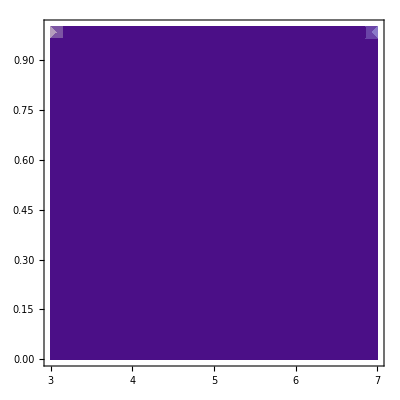

```mathematica
DensityPlot[pTargetComp[x,y],{x,3,7},{y,0,1}]
```

```mathematica
Sum[f[x,y],{x,3,7},{y,0,1}]
```

```mathematica
Sum[pComp[x],{x,0,1}]
```

30.

```mathematica
f[6.91,0]
```

InterpolatingFunction::dmval: Input value {6.91`, 0} lies outside the range of data in the interpolating function. Extrapolation will be used.

2.

```mathematica
f[6,1]
```

0.

```mathematica
Length[ftarscomps]
```

1414

```mathematica
Length[fbincounts]
```

1414

```mathematica
tars=Table[i,{i,firstTarget,lastTarget+(2*targetBinSize,targetBinSize}]
```

{3.,3.3,3.6,3.9,4.2,4.5,4.8,5.1,5.4,5.7,6.,6.3,6.6,6.9,7.2}

```mathematica
comps=Table[i,{i,0,1,compBinSize}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
targetbins
```

{3.,3.3,3.6,3.9,4.2,4.5,4.8,5.1,5.4,5.7,6.,6.3,6.6,6.9,7.2,7.5}

```mathematica
List[{"N1","N2"},{1,2}]
```

{{N1,N2},{1,2}}

```mathematica
t
```

{{N1,1},{N2,2}}

```mathematica
t[[1]]
```

{N1,1}

```mathematica
t[["N1"]]
```

Part::pspec: Part specification N1 is neither an integer nor a list of integers.

{{N1,1},{N2,2}}⟦N1⟧

```mathematica
{plot,{bincounts}}=Reap[Histogram3D[RandomReal[NormalDistribution[0,1],{100,2}],{-2,2,0.25},Function[{xbins,ybins,counts},Sow[counts]]]];
```

```mathematica
Reap[Histogram3D[RandomReal[NormalDistribution[0,1],{100,2}],{-2,2,0.25},"Count"]]
```

{-Graphics3D-,{}}

```mathematica
bincounts[[1]]
```

{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,2,0,0,0,0,1,0,1,0,0,0,0,0},{0,1,0,0,0,1,0,1,0,3,2,0,0,0,1,0},{0,0,1,0,1,1,0,0,1,0,0,0,0,1,0,0},{0,1,0,0,0,0,2,0,0,0,1,0,0,0,0,0},{0,0,2,0,2,0,1,1,1,1,0,0,4,0,1,0},{0,0,2,2,0,0,3,0,0,1,1,1,0,0,0,0},{0,0,0,1,0,1,0,0,2,1,0,0,0,1,0,0},{0,0,1,1,0,1,1,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,1,0,3,0,1,0,2,2,1,0},{0,0,1,0,0,0,0,3,0,0,0,0,0,0,0,0},{0,0,1,1,0,1,2,0,1,0,0,0,0,0,2,0},{0,0,0,0,1,1,1,1,1,0,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0}}

```mathematica
Comp="N1";
pos=Position[{"N1","N2"},Comp][[1]][[1]];
l[[pos]]
```

N1

```mathematica
pos
```

1

```mathematica
l[[1]]
```

N1

```mathematica
l={"N1","N2"};
```

```mathematica
l[[Position[l,"N1"]]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

```mathematica
l[{1}]
```

l[{1}]

```mathematica
l[[{1}]]
```

Part::partd: Part specification l ⟦ {1} ⟧ is longer than depth of object.

l⟦{1}⟧